```mathematica
Clear["`*"]
```

```mathematica
<<PlotLegends`
```

```mathematica
<<ODE`
```

To get more information type ?ODE

# Physics 318

## Homework

```mathematica
StringJoin
```

2.1

## 1.1.1-1.1.2

```mathematica
sn[n_,a_,r_]:=(a(1-r^n))/(1-r) (*sum of first nth terms in infinite series*)
s [r_,a0_]:=a0/(1-r) (*sum of infinite series where a0 is first term *)
```

```mathematica
s[2/3,(2/3)^10]*2//N
```

0.104049

## 1.6.15

```mathematica
Integrate[1/n^p,n]
```

n^(1-p)/(1-p)

## Additional Problems

```mathematica
Manipulate[(2*n*(2*n+1))/(3*n+5),{n,1,6,1}]
Manipulate[(n!)^2/((2*n)!),{n,1,6,1}]
Manipulate[n!,{n,1,10,1}]
Manipulate[(n!)/((n+2)!),{n,1,4,1}]
Manipulate[n/(2n+5),{n,1,5,1}]
Manipulate[(-1)^n/2^n,{n,2,5,1}]
```

```mathematica
D[Cos[x],x]
```

-sin(x)

```mathematica
Manipulate[D[Log[1+x],{x,n}],{n,1,5,1}]
```

```mathematica
Log[1]
```

0

```mathematica
((n+1)!)^2/(n!)^2//FullSimplify
```

(n+1)^2

```mathematica
(n+1)^(n+1)/n^n//FullSimplify
```

n^-n (n+1)^(n+1)

```mathematica
Limit[(n+1)^2/((2*n+2)(2 n+1)),n->x]
```

(x+1)/(4 x+2)

```mathematica
Manipulate[D[(1+x)^p,{x,n}],{n,0,5,1}]
```

```mathematica
120^2
```

14400

```mathematica
Expand[(2*n)!]
```

(2 n)!

2.2

2.2

```mathematica
Clear["`*"]
```

## Additional Problems # 6

```mathematica
mcsin = Table[Series[Sin[x],{x,0,n}],{n,1,7,2}]//Normal;
mccos= Table[Series[Cos[x],{x,0,n}],{n,0,6,2}]//Normal;
mcexp = Table[Series[Exp[x],{x,0,n}],{n,0,3}]//Normal;
mclog = Table[Series[Log[x+1],{x,0,n}],{n,0,3}]//Normal;
mcpoly = Table[Series[(1+x)^(1/2),{x,0,n}],{n,0,3}]//Normal
```

{1,x/2+1,-x^2/8+x/2+1,x^3/16-x^2/8+x/2+1}

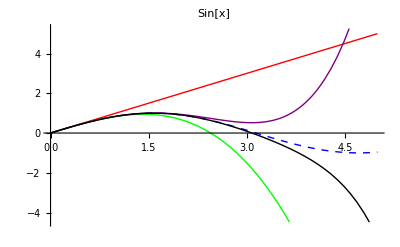

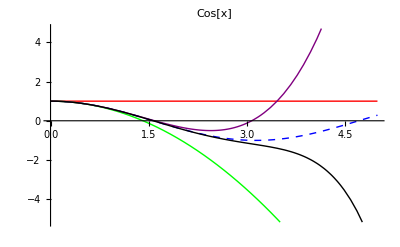

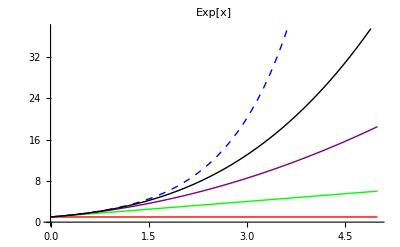

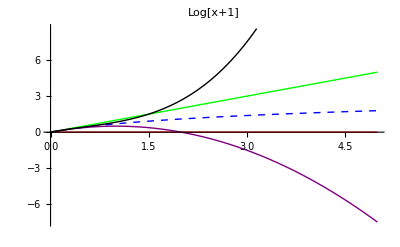

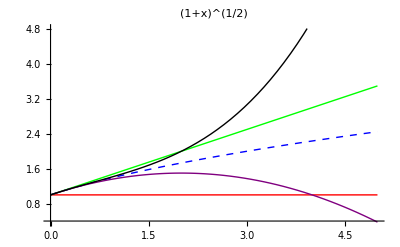

```mathematica
Plot[{Sin[x],mcsin},{x,0,5},PlotStyle->{{Thick,Dashed,Blue},Red,Green,Purple,Black},PlotLabel->"Sin[x]"]
Plot[{Cos[x],mccos},{x,0,5},PlotStyle->{{Thick,Dashed,Blue},Red,Green,Purple,Black},PlotLabel->"Cos[x]"]
Plot[{Exp[x],mcexp},{x,0,5},PlotStyle->{{Thick,Dashed,Blue},Red,Green,Purple,Black},PlotLabel->"Exp[x]"]
Plot[{Log[x+1],mclog},{x,0,5},PlotStyle->{{Thick,Dashed,Blue},Red,Green,Purple,Black},PlotLabel->"Log[x+1]"]
Plot[{√(x+1),mcpoly},{x,0,5},PlotStyle->{{Thick,Dashed,Blue},Red,Green,Purple,Black},PlotLabel->"(1+x)^(1/2)"]
```

3.1

## 2.4.3

```mathematica
ArcTan[1,-√3]
```

-π/3

```mathematica
1/(I-1)
```

-1/2-ⅈ/2

```mathematica
√((1/2)^2+(1/2)^2)
```

1/(√2)

```mathematica
ArcTan[(-1/2)/(-1/2)]
```

π/4

```mathematica
25*Cos[2]//N
25*Sin[2]//N
```

-10.4037

22.7324

```mathematica
(3*I-7)/(I+4)
```

-25/17+(19 ⅈ)/17

```mathematica
ArcTan[(25*Sin[2])/(25*Cos[2])]
```

2-π

```mathematica
(1+x+I*y)/(1-x-I*y)//FullSimplify
```

-1-2/(x+ⅈ y-1)

```mathematica
Abs[1-(x+I*y)]//Simplify
```

Abs[-x-ⅈ y+1]

```mathematica
(1-x)^2//Expand
```

x^2-2 x+1

3.3

## 2.6.5-12

```mathematica
Integrate[1/n^2,n]
Integrate[1/n,n]
```

-1/n

log(n)

```mathematica
Log[∞]
```

∞

```mathematica
(3+2*I)^n/(n!)//ComplexExpand
```

(13^(n/2) cos(n tan^-1(2/3)))/(n!)+(ⅈ 13^(n/2) sin(n tan^-1(2/3)))/(n!)

```mathematica
(n!)/((n+1)!)//FullSimplify
```

1/(n+1)

## 2.7.7-16

```mathematica
Exp[2*(n+1)]//ComplexExpand
```

ⅇ^(2 n+2)

```mathematica
((2n)!)/((2 (n+1))!)//FullSimplify
```

1/(4 n^2+6 n+2)

```mathematica
Limit[(((-1)^(n+1)*z^(2n+2)*(2n)!)/((2n+2)!*(-1)^n*z^(2n))) ,n->∞]
```

0

```mathematica
Limit[(2^(n+1)*(z-3+I)^(2*(n+1)))/(2^n*(z-3+I)^(2*n)),n->∞]
```

2 (z-(3-ⅈ))^2

```mathematica
1/√2.0
```

0.707107

```mathematica
Exp[1]
```

ⅇ

```mathematica
Cos[4*π/3]
Sin[4*π/3]
```

-1/2

-(√3)/2

```mathematica
ExpToTrig[Exp[(1/3)*(2+4*π*I)]]//N
```

-0.973867-1.68679 ⅈ

```mathematica
Exp[1]*-1/2//N
```

-1.35914

```mathematica
ArcTan[-√3]
```

-π/3

```mathematica
2/√2
```

√2

```mathematica
38/4
```

19/2

```mathematica
(√2)^38
```

524288

```mathematica
2^19
```

524288

```mathematica
2^21/2^19
```

4

```mathematica
Manipulate[Abs[Exp[I*y]],{y,1,1000,1}]
```

```mathematica
Exp[π*I/2]
```

ⅈ

```mathematica
√I
```

-1^(1/4)

```mathematica
Abs[I]
```

1

```mathematica
1^(1/2)
```

1

```mathematica
Cos[π/4]
```

1/(√2)

```mathematica
(√8)^(1/3)
```

√2

```mathematica
(1+I)^3
```

-2+2 ⅈ

```mathematica
Cos[19*π/12]*√2+Sin[19*π/12]*√2*I
```

1/2 (√3-1)-1/2 ⅈ (1+√3)

```mathematica
Exp[2*x]^2
```

ⅇ^(4 x)

```mathematica
Limit[((y^n 2^n)/(3^n+n^3)*(3^(n+1)(n+1)^3)/(y^(n+1)2^(n+1))),n->∞]
```

∞/y

```mathematica
(n!)^2/((n+1)!)^2//FullSimplify
```

1/(n+1)^2

```mathematica
((y^n 2^n)/(3^n+n^3)*(3^(n+1)(n+1)^3)/(y^(n+1)2^(n+1)))//FullSimplify
```

(3^(n+1) (n+1)^3)/(2 (n^3+3^n) y)

```mathematica
((n+1)!)/(n!)//FullSimplify
```

n+1

3.4

```mathematica
Factor[(Exp[I*x]*Exp[I*(I*y)]-Exp[-I*x]*Exp[-I*(I*y)])/(2*I)]//Expand
```

1/4 ⅈ ⅇ^(y-ⅈ x)-1/4 ⅈ ⅇ^(-y+ⅈ x)

```mathematica
(Exp[I*x]*Exp[I*(I*y)]-Exp[-I*x]*Exp[-I*(I*y)])/(4*I)
```

-1/4 ⅈ (ⅇ^(-y+ⅈ x)-ⅇ^(y-ⅈ x))

```mathematica
ExpToTrig[(Exp[I*(x+I*y)]-Exp[-I*(x+I*y)])/(2*I)]//ComplexExpand
```

sin(x) cosh(y)+ⅈ cos(x) sinh(y)

```mathematica
Factor[(x*y-1/(x*y))/(4*I)]
```

-(ⅈ (x y-1) (x y+1))/(4 x y)

```mathematica
ComplexExpand[Exp[-x*I]]//ExpToTrig
```

cos(x)-ⅈ sin(x)

```mathematica
Sin[I*x-y]/Cos[I*x-y]
```

ⅈ tanh(x+ⅈ y)

```mathematica
Cosh[I*x]
```

cos(x)

```mathematica
Cos[3*π/4]
```

```mathematica
-1/(√2)
```

```mathematica
Tanh[I*3*π/4]
```

-ⅈ

```mathematica
(2)Exp[I*(2π/3)]//ExpToTrig
```

-1+ⅈ √3

```mathematica
Solve[ω*L-1/(ω*C)==r,ω]
```

{{ω→(C r-√C √(C r^2+4 L))/(2 C L)},{ω→(√C √(C r^2+4 L)+C r)/(2 C L)}}

```mathematica
1/(I*L*ω*cur)
```

-ⅈ/(cur L ω)

```mathematica
c = 1/(I*ω*cap)*cur
```

-(ⅈ cur)/(cap ω)

```mathematica
1/c
```

(ⅈ cap ω)/cur

```mathematica
Cos[π/6]
```

(√3)/2

```mathematica
Tan[π/4]
```

1

```mathematica
Clear["`*"]
```

```mathematica
hi = (1/cur((l ω +I l c r ω^2-I r)/(r l ω)))^-1//ComplexExpand
```

(cur l^2 r ω^2)/((c l r ω^2-r)^2+l^2 ω^2)+ⅈ ((cur l r^2 ω)/((c l r ω^2-r)^2+l^2 ω^2)-(c cur l^2 r^2 ω^3)/((c l r ω^2-r)^2+l^2 ω^2))

```mathematica
Re[hi]
```

Re((cur l^2 r ω^2)/((c l r ω^2-r)^2+l^2 ω^2))-Im((cur l r^2 ω)/((c l r ω^2-r)^2+l^2 ω^2)-(c cur l^2 r^2 ω^3)/((c l r ω^2-r)^2+l^2 ω^2))

```mathematica
Solve[(cur l^2 r ω^2)/((c l r ω^2-r)^2+l^2 ω^2) == ((cur l r^2 ω)/((c l r ω^2-r)^2+l^2 ω^2)-(c cur l^2 r^2 ω^3)/((c l r ω^2-r)^2+l^2 ω^2)),ω]
```

{{ω→0},{ω→(-√l √(4 c r^2+l)-l)/(2 c l r)},{ω→(√l √(4 c r^2+l)-l)/(2 c l r)}}

```mathematica
Manipulate[π/4+2 π m,{{m,0},-2,2,1}]
```

```mathematica
ArcTan[1]
```

π/4

## 2.16.10

### a.)

```mathematica
zr = cur*R;
zl = I*ω*L*cur;
zc = cur/(i*ω*c);
```

```mathematica
(*this is where I left off on the paper *)
```

```mathematica
paper =(1/cur((l ω +I l c r ω^2-I r)/(r l ω)))^-1//ComplexExpand
```

(cur l^2 r ω^2)/((c l r ω^2-r)^2+l^2 ω^2)+ⅈ ((cur l r^2 ω)/((c l r ω^2-r)^2+l^2 ω^2)-(c cur l^2 r^2 ω^3)/((c l r ω^2-r)^2+l^2 ω^2))

```mathematica
(* as before the ArcTan[Im[z]/Re[z]]=π/4 ->Im[z]/Re[z]=1 -> Im[z] = Re[z] *)
answer = Solve[(cur l^2 r ω^2)/((c l r ω^2-r)^2+l^2 ω^2)==(cur l r^2 ω)/((c l r ω^2-r)^2+l^2 ω^2)-(c cur l^2 r^2 ω^3)/((c l r ω^2-r)^2+l^2 ω^2),ω]
```

{{ω→0},{ω→(-√l √(4 c r^2+l)-l)/(2 c l r)},{ω→(√l √(4 c r^2+l)-l)/(2 c l r)}}

```mathematica
(* we want the nonzero (+) answer so we will select the third one *)
ω/.answer[[3]]
```

(√l √(4 c r^2+l)-l)/(2 c l r)

### b.)

Again, as in #9, we set Z_L = Z_C so we get the same answer as in #9, that is ω  = 1/(√LC)

## Additional Problem 4

### a.)

```mathematica
zin = ((ω r^2)/k+m ω (m/k ω^2-1))/((m/k ω^2-1)^2+r^2/k^2 ω^2)
```

(m ω ((m ω^2)/k-1)+(r^2 ω)/k)/((r^2 ω^2)/k^2+((m ω^2)/k-1)^2)

```mathematica
ω/.Solve[zin==0,ω][[3]]
```

(√(k m-r^2))/m

f is equal to ω/2π and if you take the m into the square root you get the following...

```mathematica
ans = 1/(2π)√(k/m-(r/m)^2);
```

### b.)

```mathematica
ans/.{r->0.01,m->1,k->1*^4}
```

15.9155

4.1

### 7.2.20

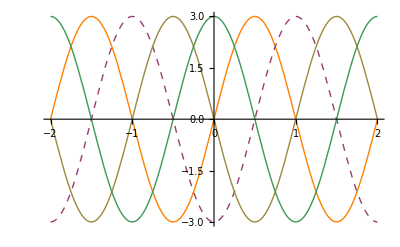

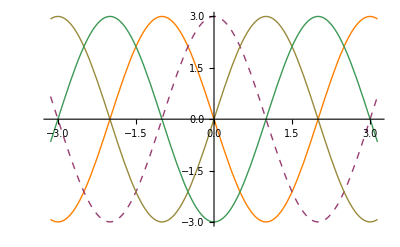

```mathematica
y20 = 3*Sin[π*x-π/2*t];
xs = Range[0,2,1/2];
ts = Range[0,3,1];
plotFixedt = Table[y20/.t->ts[[i]],{i,1,4}];
Plot[plotFixedt,{x,-2,2},PlotStyle->{{Orange},{Dashed},{Thick},{Thin}}]
plotFixedx = Table[y20/.x->xs[[i]],{i,1,4}];
Plot[plotFixedx,{t,-π,π},PlotStyle->{{Orange},{Dashed},{Thick},{Thin}}]
```

### Additional Problems 1

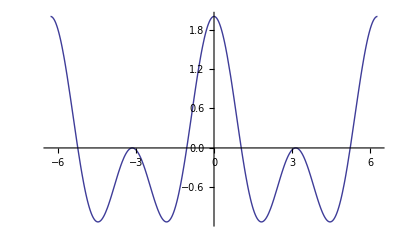

```mathematica
Plot[Cos[x]+Cos[2 x],{x,-2π,2π}]
```

```mathematica
Cos[x]+Cos[2 x]//FullSimplify
```

cos(x)+cos(2 x)

### Additional Problems 2

#### a.)

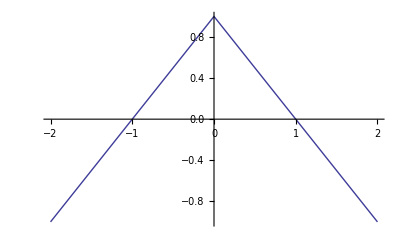

```mathematica
Plot[Piecewise[{{x+1,-2≤x≤0},{-x+1,0<x≤2}}],{x,-2,2}]
```

```mathematica
Cos[3*
```

4.2

### 7.3.3

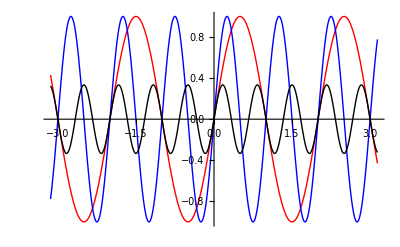

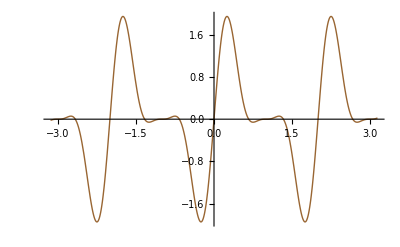

```mathematica
Plot[{Sin[π t],Sin[2π t], Sin[3 π t]/3},{t,-π,π},PlotStyle->{Red,Blue,Black}]
Plot[Sin[π t]+Sin[2π t]+ Sin[3 π t]/3,{t,-π,π},PlotStyle->{Brown,Thick}]
```

### 7.3 .6

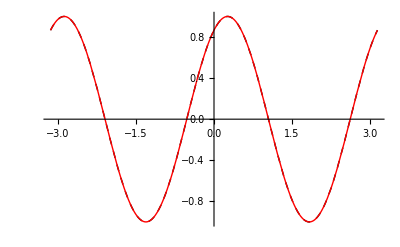

```mathematica
Plot[{Sin[2 x]+Sin[2(x + π/3)],Sin[2 x+π/3]},{x,-π,π},PlotStyle->{{Dashed,Black,Thick},{Red,Thick}}]
```

### 7.3.8

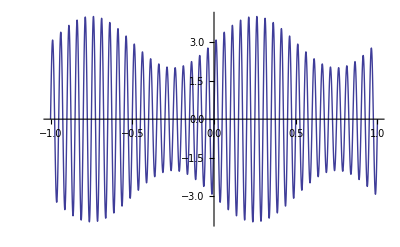

```mathematica
Plot[(3+Sin[2 π t])*Sin[40 π t],{t,-1,1}]
```

4.3

### Additional Problem 1

```mathematica
f[x_,m_]:=1/4+∑_(n=1)^m ((-1)^(n-1)Cos[(2n-1)x])/(π(2n-1))+∑_(n=1)^m (Sin[(2n-1)x]+Sin[2(2n-1)x])/(π(2n-1))
```

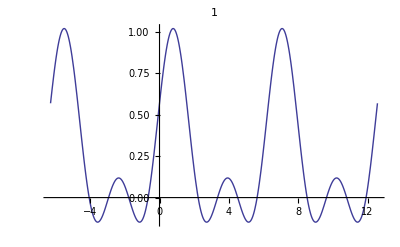
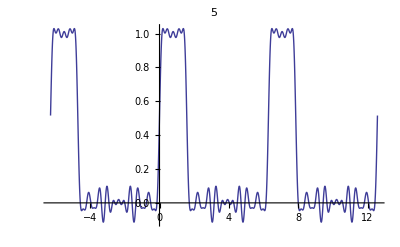
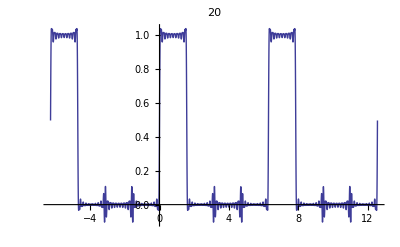
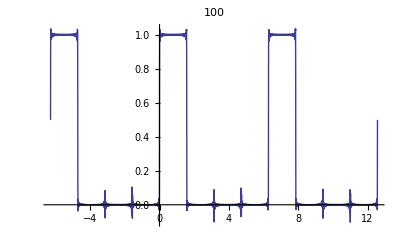

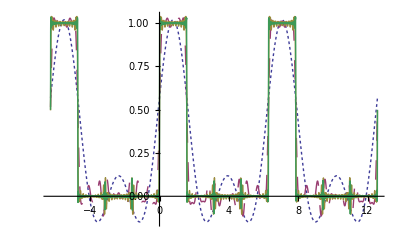

```mathematica
Table[Plot[f[x,m],{x,-2π,4π},PlotLabel->m],{m,{1,5,20,100}}]
Plot[{f[x,1],f[x,5],f[x,20],f[x,100]},{x,-2π,4π},PlotLegend->{"1 term","5 terms","20 terms","100 terms"},PlotStyle->{Dashing[Tiny],Dashing[Large],Thin,{}}]
```

### Additional Problem 2

```mathematica
g[x_,m_]:=π/4-2/π∑_(n=1)^m Cos[(2n-1)]/(2n-1)^2+∑_(n=1)^m ((-1)^(n-1)Sin[n x])/n
```

```mathematica
g[x,3]
```

sin(x)-1/2 sin(2 x)+1/3 sin(3 x)+π/4-(2 cos(5))/(25 π)-(2 cos(3))/(9 π)-(2 cos(1))/π

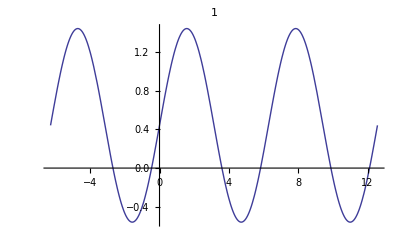
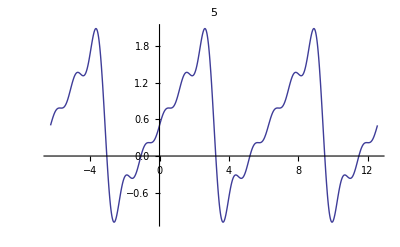
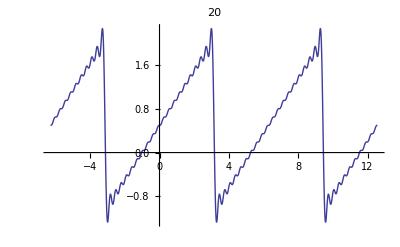
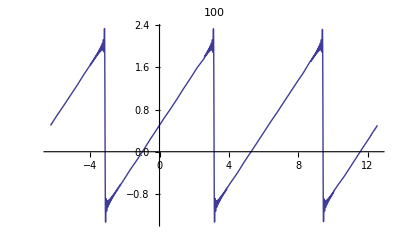

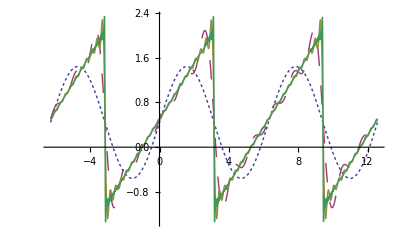

```mathematica
Table[Plot[g[x,m],{x,-2π,4π},PlotLabel->m],{m,{1,5,20,100}}]
Plot[{g[x,1],g[x,5],g[x,20],g[x,100]},{x,-2π,4π},PlotLegend->{"1 term","5 terms","20 terms","100 terms"},PlotStyle->{Dashing[Tiny],Dashing[Large],Thin,{}}]
```

### Additional Problem 3

```mathematica
h[x_,m_]:=1/π+Sin[x]/2-2/π∑_(n=1)^m Cos[2 n x]/((2n)^2-1)
```

```mathematica
h[x,4]
```

(sin(x))/2-(2 (1/3 cos(2 x)+1/15 cos(4 x)+1/35 cos(6 x)+1/63 cos(8 x)))/π+1/π

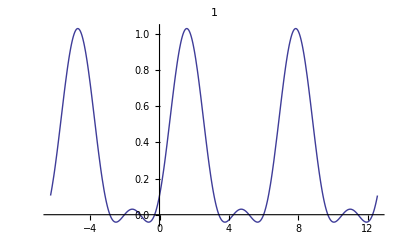
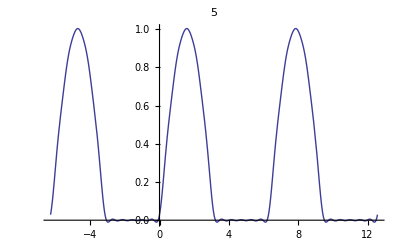
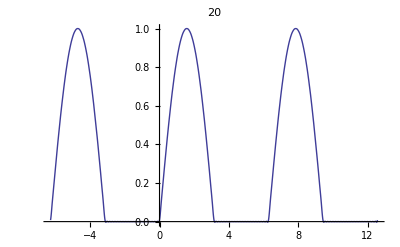
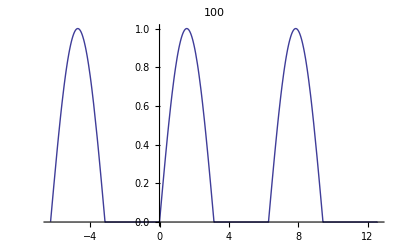

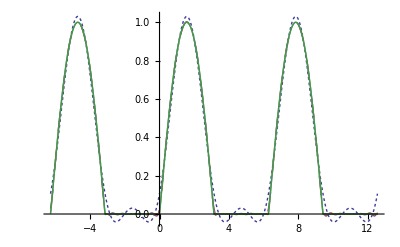

```mathematica
Table[Plot[h[x,m],{x,-2π,4π},PlotLabel->m],{m,{1,5,20,100}}]
Plot[{h[x,1],h[x,5],h[x,20],h[x,100]},{x,-2π,4π},PlotLegend->{"1 term","5 terms","20 terms","100 terms"},PlotStyle->{Dashing[Tiny],Dashing[Large],Thin,{}}]
```

4.6

### 7.10.1

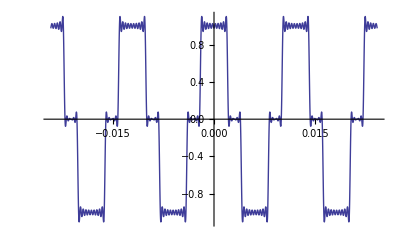

```mathematica
Plot[∑_(n=1)^30 2/(n π)*(Sin[n π/3]- Sin[n π]+Sin[2n π /3])*Cos[165 n π x],{x,-4/165,4/165}]
```

4.7

### Additional Problem 1

#### Part b

```mathematica
f0 = 25; to = 1/f0;
```

```mathematica
Hw[ω_]= √(1/(2π))(((ω0+ω)Sin[t0(ω0 - ω)]+ (ω0-ω)*Sin[t0(ω0+ω)])/(ω0^2-ω^2));
```

```mathematica
Hf[f_] = Hw[f*2π]/.ω0->f0 2π
h[t_] = Piecewise[{{Cos[2π f0*t],-t0<t<t0},{0,t≥t0},{0,t≤-t0}}]
```

((2 π f+50 π) sin((50 π-2 π f) t0)+(50 π-2 π f) sin((2 π f+50 π) t0))/(√(2 π) (2500 π^2-4 π^2 f^2))

Piecewise[{{cos(50 π t), -t0<t<t0}, {0, True}}]

```mathematica
t0s = Table[to*i,{i,{.01,.1,1,5,10,100,1000,10000}}]/2;
```

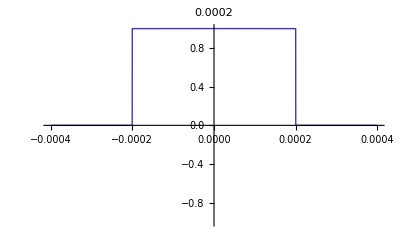
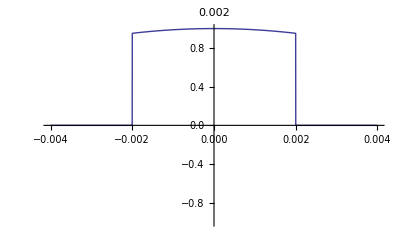
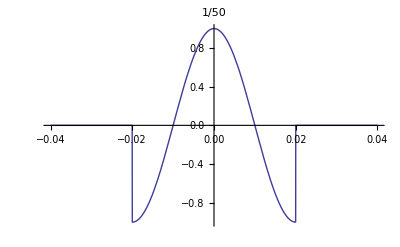
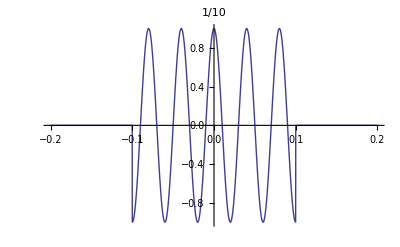
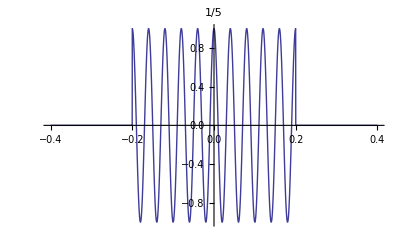
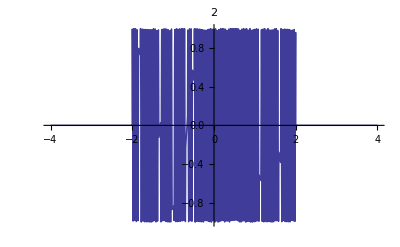
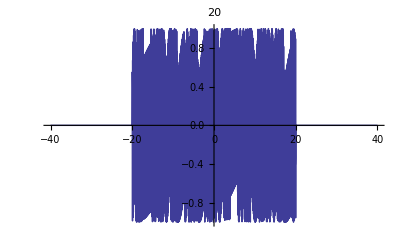
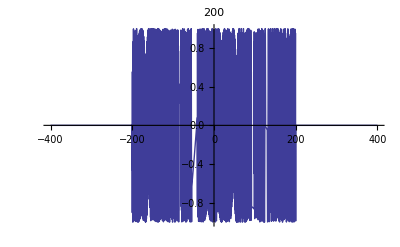

```mathematica
Table[Plot[h[t]/.t0->t0s[[i]],{t,-2*t0s[[i]],2*t0s[[i]]},PlotLabel->t0s[[i]],PlotRange->{-1,1}],{i,1,8}]
Table[Plot[Hf[f]/.t0->t0s[[i]],{f,-4f0,4f0},PlotRange->{0,0.05}],{i,1,8}]
```

5.3

```mathematica
InverseLaplaceTransform[p/((p+a)(p+b)^2),p,t]
```

-(a ⅇ^(-a t))/(a-b)^2+(a ⅇ^(-b t))/(a-b)^2-(b ⅇ^(-b t) t)/(a-b)

```mathematica
Integrate[Exp[-a*(t-τ)]*Exp[-b*τ]*(1-b*τ),τ]
```

(ⅇ^(-a t+a τ-b τ) (a-a b τ+b^2 τ))/(a-b)^2

```mathematica
Exp[-a*(t-τ)]*Exp[-b*τ]*(1-b*τ)//Simplify
```

ⅇ^(-a t+a τ-b τ) (1-b τ)

```mathematica
Integrate[b*τ*Exp[τ (a-b)],τ]
```

(b ⅇ^((a-b) τ) (-1+a τ-b τ))/(a-b)^2

```mathematica
LaplaceTransform[y''[x]-a^2 *y[x],y,s]
```

-(a^2 y[x])/s+y''[x]/s

```mathematica
InverseLaplaceTransform[1/(s^2-a^2),s,t]//FullSimplify
```

Sinh[a t]/a

```mathematica
DSolve[{y''[t]-a^2 y[t]==Piecewise[{{1,t>0}}],y[0]==0,y'[0]==0},y[t],t]//FullSimplify
```

{{y[t]→Piecewise[{{0, t≤0}, {(-1+Cosh[a t])/a^2, True}}]}}

```mathematica
Piecewise[{{1,t>0}}]
```

Piecewise[{{1, t>0}, {0, True}}]

```mathematica
ⅇ^(a t) C[1]+ⅇ^(-a t) C[2]//ExpToTrig//FullSimplify
```

ⅇ^(a t) C[1]+ⅇ^(-a t) C[2]

```mathematica
Cosh[0]
```

1

```mathematica
DSolve[{y''[x]+ω^2 y[x]==Piecewise[{{1,0<t<a}}],y[0]==0,y'[0]==0},y[x],x]
```

{{y[x]→((Piecewise[{{1, 0<t<a}, {0, True}}])-Cos[x ω] (Piecewise[{{1, 0<t<a}, {0, True}}]))/ω^2}}

```mathematica
`
```

5.4

### 8.11.9

```mathematica
DSolve[{y''[x]+2y'[x]+10y[x]==DiracDelta[x-x0],y[0]==0,y'[0]==0},y[x],x]//TraditionalForm//FullSimplify
```

{{y(x)→1/3 ⅇ^(x0-x) (x-x0--x0) sin(3 (x-x0))}}

```mathematica
x^2+2x+10//Factor
```

10+2 x+x^2

```mathematica
(x+1)^2+8//Expand
```

9+2 x+x^2

```mathematica
InverseLaplaceTransform[Exp[-p*a]*1/((p+1)^2+9),p,t]//TraditionalForm//FullSimplify
```

-1/3 ⅇ^(a-t) t-a sin(3 (a-t))

```mathematica
Integrate[Sin[x]*DiracDelta[x+π/2],{x,0,π}]
```

0

### Additional Problem 1

```mathematica
t0 = 0.5;
```

```mathematica
rectangular[n_,t_]:=Piecewise[{{n,-1/(2n)<t-t0<1/(2n)}}]
resonance[n_,t_]:=n/((1+n^2(t-t0)^2)π)
sincSquared[n_,t_]:= Sin[n(t-t0)]^2/(n π (t-t0)^2)
gaussian [n_,t_]:= n/(√π)Exp[-n^2(t-t0)^2]
```

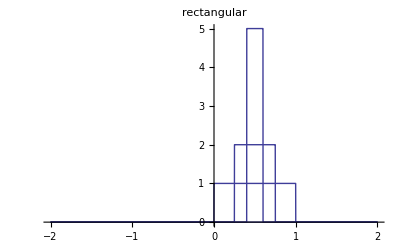

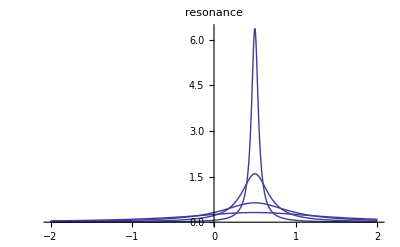

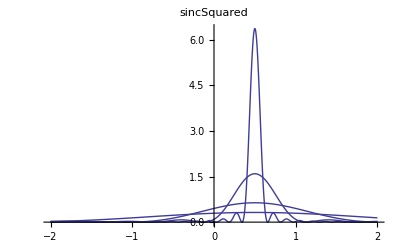

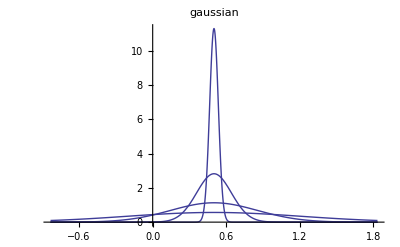

```mathematica
Plot[Table[rectangular[n,t],{n,{1,2,5,20}}],{t,-2,2},PlotLabel->"rectangular"]
Plot[Table[resonance[n,t],{n,{1,2,5,20}}],{t,-2,2},PlotLabel->"resonance",PlotRange->All]
Plot[Table[sincSquared[n,t],{n,{1,2,5,20}}],{t,-2,2},PlotLabel->"sincSquared",PlotRange->All]
Plot[Table[gaussian[n,t],{n,{1,2,5,20}}],{t,-2,2},PlotLabel->"gaussian",PlotRange->All]
```

```mathematica
Plot[rectangular[1,t],{t,-1,1}]
```

-Graphics-

```mathematica
Integrate[Table[rectangular[n,t],{n,{1,2,5,20}}],{t,-∞,∞}]
Integrate[Table[resonance[n,t],{n,{1,2,5,20}}],{t,-∞,∞}]//Simplify
Integrate[Table[sincSquared[n,t],{n,{1,2,5,20}}],{t,-∞,∞}]
Integrate[Table[gaussian[n,t],{n,{1,2,5,20}}],{t,-∞,∞}]
```

{1.,1.,1.,1.}

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

{1.-7.34568×10^-17 ⅈ,1.-2.51084×10^-16 ⅈ,1.-1.53083×10^-15 ⅈ,1.-2.44929×10^-14 ⅈ}

```mathematica
Piecewise[{{n,-1/(2n)<t-t0<1/(2n)}}]
```

Piecewise[{{n, -1/(2 n)<t-0.5<1/(2 n)}, {0, True}}]

Exam 1

### 3.)

#### a.)

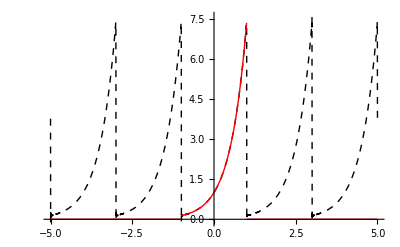

```mathematica
Plot[{Re[Sinh[2] * Sum[(-1)^n/(2 - I π n)*Exp[I π n x],{n,-1000,1000}]],Piecewise[{{Exp[2*x],-1<x<1}}]},{x,-5,5},PlotStyle->{{Dashed,Thick,Black},{Red}}]
```

#### b.)

```mathematica
dataSin = -2 Sinh[ 2] π * Sum[((-1)^n n)/((2)^2+(n π)^2)*Sin[n π x],{n,1,20}] + 4Sinh[2] * Sum[(-1)^n/(4+(π n )^2)*Cos[n π x],{n,1,20}]+4Sinh[2]/8;
```

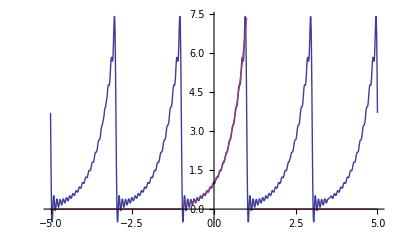

```mathematica
Plot[{dataSin,Piecewise[{{Exp[2*x],-1<x<1}}]},{x,-5,5}]
```

### 4.)

#### a.)

```mathematica
dataCos = -4/π Sum[Cos[(2n-1)x]/(2n-1)^2,{n,1,20}];
```

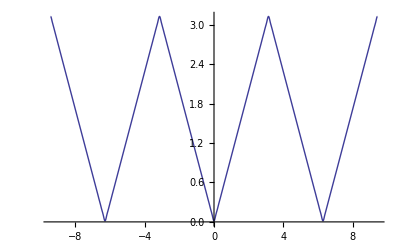

```mathematica
Plot[dataCos+π/2,{x,-3π,3π}]
```

### 5.)

#### b.)

```mathematica
expression = b^2+(a+ⅈ ω)^2;
```

```mathematica
top =Simplify[(a+I ω)*Conjugate[expression],Assumptions->{a∈Reals,b∈Reals,ω∈Reals}]//Expand;
bottom = Simplify[expression *Conjugate[expression],Assumptions->{a∈Reals,b∈Reals,ω∈Reals}]//Expand;
```

```mathematica
X = Refine[A/(2π) * (Re[top]/bottom+I Im[top]/bottom),Assumptions->{a∈Reals,b∈Reals,ω∈Reals,A∈Reals}]
```

(A ((a^3+a b^2+a ω^2)/(a^4+2 a^2 b^2+b^4+2 a^2 ω^2-2 b^2 ω^2+ω^4)+(ⅈ (-a^2 ω+b^2 ω-ω^3))/(a^4+2 a^2 b^2+b^4+2 a^2 ω^2-2 b^2 ω^2+ω^4)))/(2 π)

```mathematica
modulus = FullSimplify[√(((A/(2 π))Re[top]/bottom)^2+((A/(2 π))Im[top]/bottom)^2),Assumptions->{a∈Reals,b∈Reals,ω∈Reals,A∈Reals}]
```

(√((a^2+ω^2)/((a^2+b^2)^2+2 (a-b) (a+b) ω^2+ω^4)) Abs[A])/(2 π)

#### d.)

```mathematica
Solve[2 ( a^2+b^2)^2 - 4 a^2(a+b)(a-b) - 4 ω^2 a^2 - 2 ω^4==0,ω]
```

{{ω→-√(-a^2-√(b^2 (4 a^2+b^2)))},{ω→√(-a^2-√(b^2 (4 a^2+b^2)))},{ω→-√(-a^2+√(4 a^2 b^2+b^4))},{ω→√(-a^2+√(4 a^2 b^2+b^4))}}

#### e.)

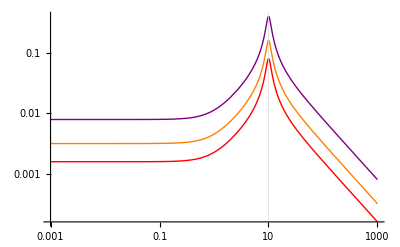

```mathematica
LogLogPlot[{modulus/.{a->1,b->10,A->1},modulus/.{a->1,b->10,A->2},modulus/.{a->1,b->10,A->5}},{ω,0.001,1000},PlotStyle->{Red,Orange,Purple},GridLines->{{√(-a^2+√(4 a^2 b^2+b^4))/.{a->1,b->10}},{}},PlotLegend->{"A = 1","A = 2","A =5"},LegendPosition->{.5,.42}]
```

```mathematica
√(-a^2+√(4 a^2 b^2+b^4))/.{a->1,b->10}//N
```

10.0489

6.1

6.2

### 1.)

```mathematica
check[x0_]:=Module[{p,q,plim,qlim},
p= (x-x0)*-2/(1-x^2);
q=(x-x0) (x+1)/(x(1-x));
plim = Limit[p,x->x0];
qlim = Limit[q,x->x0];
{plim,qlim}

]
```

```mathematica
check[-1]
check[0]
check[1]
```

{-1,0}

{0,1}

{1,-2}

### 2.)

```mathematica
check2[x0_]:=Module[{p,q,plim,qlim},
p= (x-x0)*1/(x Tan[x]);
q=(x-x0) 1/(x^2 Tan[x]);
plim = Limit[p,x->x0];
qlim = Limit[q,x->x0];
{plim,qlim}

]
```

```mathematica
check2[0]
check2[π]
check2[2π]
check2[3π]
check2[4π]
check2[5π]
```

{∞,∞}

{1/π,1/π^2}

{1/(2 π),1/(4 π^2)}

{1/(3 π),1/(9 π^2)}

{1/(4 π),1/(16 π^2)}

{1/(5 π),1/(25 π^2)}

6.3

### 12.1.1

```mathematica
LegendreP[2,x]
LegendreP[3,x]
LegendreP[4,x]
```

1/2 (3 x^2-1)

1/2 (5 x^3-3 x)

1/8 (35 x^4-30 x^2+3)

```mathematica
14*20
```

280

```mathematica
280/24
```

35/3

```mathematica
1-10+35/3
```

8/3

```mathematica
(4*5*2*7)/4!
```

35/3

```mathematica
1-10+35/3
```

8/3

```mathematica
Limit[x^2*((3 x-2)/(3x)),x->0]
```

0

```mathematica
Solve[(s-1) s + 2/3 s==0,s]
```

{{s→0},{s→1/3}}

```mathematica
(n+σ+1)(n+σ+2)*3+2(n+σ+2)/.σ->1/3
```

3 (n+4/3) (n+7/3)+2 (n+7/3)

```mathematica
6(n+σ+1)+2/.σ->1/3
```

6 (n+4/3)+2

```mathematica
rf=((6(n+σ+1) +2)bn1 - 3bn)/(3(n+σ+1)(n+σ+2) + 2(n+σ+2))
```

(bn1 (6 (n+σ+1)+2)-3 bn)/(3 (n+σ+1) (n+σ+2)+2 (n+σ+2))

```mathematica
rf/.σ->1/3//FullSimplify
```

(2 bn1 (3 n+5)-3 bn)/((n+2) (3 n+7))

6.4

### 11.3

```mathematica
ordinate =abscissa = Table[i,{i,-5,5}];
```

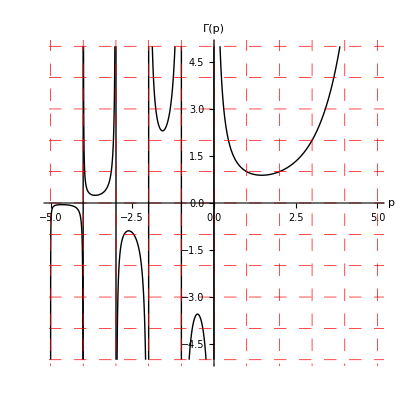

```mathematica
Plot[Gamma[p],{p,-5,5},PlotRange->{-5,5},GridLines->{abscissa,ordinate},AspectRatio->1,AxesLabel->{"p",""},PlotLabel->"Γ(p)",GridLinesStyle->Directive[Red,Dashing[Medium]],PlotStyle->{Black,Thick}]
```

7.1

### 12.14.5

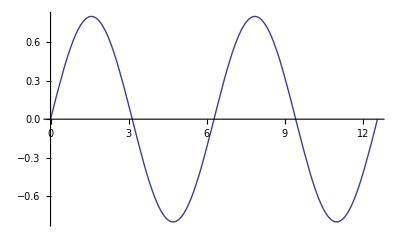

```mathematica
Plot[√x BesselJ[1/2,x],{x,0,4π}]
```

```mathematica
√x BesselJ[1/2,x]
```

√(2/π) sin(x)

### Additional Problem 1

```mathematica
j[p_,x_]:=∑_(m=0)^M ((-1)^m*(x/2)^(2m +p))/(m! Gamma[p+m+1])
```

```mathematica
y[p_,x_]:=Cos[p π]/Sin[p π] j[p,x] - 1/Sin[p π] j[-p,x]
```

#### Part a.) Print the series from page 7-6 of the lecture notes along with the built in function for M = 10, p=2/3, {x,0,20}

```mathematica
jDataA = j[2/3,x]/.M->10;jFuncA = BesselJ[2/3,x];
```

```mathematica
yDataA = y[2/3,x]/.M->10;  yFuncA = BesselY[2/3,x];
```

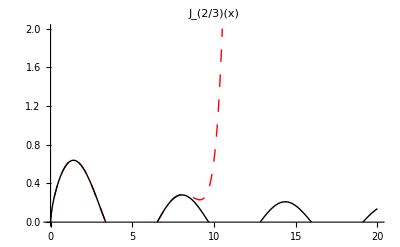

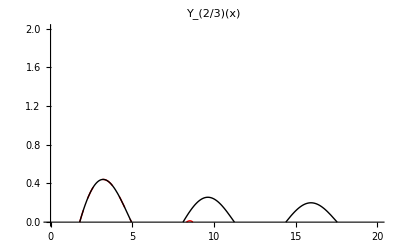

```mathematica
Plot[{jDataA,jFuncA},{x,0,20},PlotStyle->{{Dashing[Medium],Red,Thick},{Black}},PlotRange->{0,2},PlotLegend->{"Series Approx.","Built in Function"},LegendPosition->{.4,0},LegendShadow->False,LegendSize->.75,PlotLabel->"J_(2/3)(x)"]

Plot[{yDataA,yFuncA},{x,0,20},PlotStyle->{{Dashing[Medium],Red,Thick},{Black}},PlotRange->{0,2},PlotLegend->{"Series Approx.","Built in Function"},LegendPosition->{.4,0},LegendShadow->False,LegendSize->.75,PlotLabel->"Y_(2/3)(x)"]
```

#### Part b.) Print the series from page 7-6 of the lecture notes along with the built in function for M = 15, p=1/100, {x,0,20}

```mathematica
jDataB = j[1/100,x]/.M->15;jFuncB = BesselJ[1/100,x];
```

```mathematica
yDataB = y[1/100,x]/.M->15;  yFuncB = BesselY[1/100,x];
```

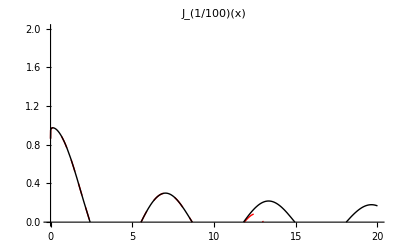

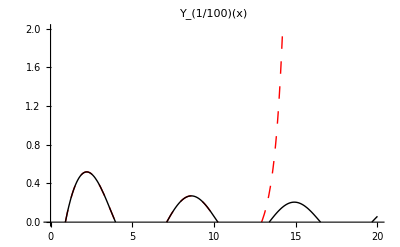

```mathematica
Plot[{jDataB,jFuncB},{x,0,20},PlotStyle->{{Dashing[Medium],Red,Thick},{Black}},PlotRange->{0,2},PlotLegend->{"Series Approx.","Built in Function"},LegendPosition->{.4,0},LegendShadow->False,LegendSize->.75,PlotLabel->"J_(1/100)(x)"]

Plot[{yDataB,yFuncB},{x,0,20},PlotStyle->{{Dashing[Medium],Red,Thick},{Black}},PlotRange->{0,2},PlotLegend->{"Series Approx.","Built in Function"},LegendPosition->{.4,0},LegendShadow->False,LegendSize->.75,PlotLabel->"Y_(1/100)(x)"]
```

7.2

### 12.17.10

#### a.)

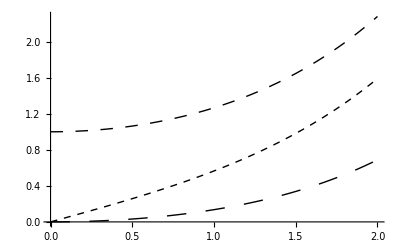

```mathematica
Plot[{bessels[i][0, x], BesselI[1, x], BesselI[2, x]}, {x, 0, 2}, PlotStyle -> {{Dashing[Medium], Black, Thick}, {Dashing[Small], Black, Thick}, {Dashing[Large], Black, Thick}}, PlotLegend -> {BesselI[0, x], BesselI[1, x], BesselI[2, x]}, LegendPosition -> {1, -0.25}]
```

#### b.)

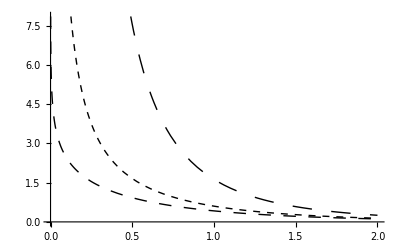

```mathematica
Plot[{BesselK[0,x], BesselK[1, x], BesselK[2, x]}, {x, 0, 2}, PlotStyle -> {{Dashing[Medium], Black, Thick}, {Dashing[Small], Black, Thick}, {Dashing[Large], Black, Thick}}, PlotLegend -> {BesselK[0, x], BesselK[1, x], BesselK[2, x]}, LegendPosition -> {1, -0.25}]
```

#### c.)

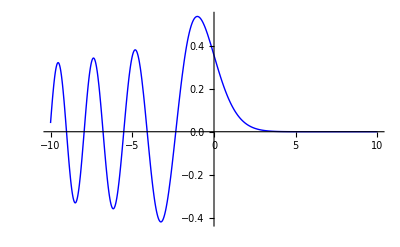

```mathematica
Plot[AiryAi[x],{x,-10,10},PlotStyle->{Thick,Blue},PlotLegend->AiryAi[x]]
```

#### d.)

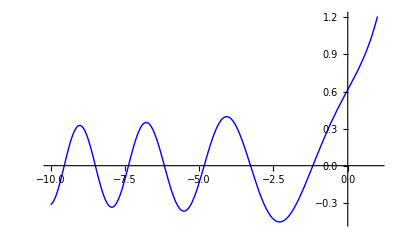

```mathematica
Plot[AiryBi[x],{x,-10,1},PlotStyle->{Blue,Thick},PlotLegend->AiryBi[x]]
```

### Additional Problem 2

```mathematica
D[(π/(2x))^(1/2)Jj[x],x]//FullSimplify
D[(-1)^(n+1)(π/(2x))^(1/2)Jy[x],x]//FullSimplify
```

1/2 √(π/2) (1/x)^(3/2) (2 x Jj'(x)-Jj(x))

1/2 √(π/2) (-1)^n (1/x)^(3/2) (Jy(x)-2 x Jy'(x))

```mathematica
w = ({{(π/(2x))^(1/2)Jj[x], (-1)^(n+1)(π/(2x))^(1/2)Jy[x]}, {D[(π/(2x))^(1/2)Jj[x],x], D[(-1)^(n+1)(π/(2x))^(1/2)Jy[x],x]}})
```

(√(π/2) √(1/x) Jj(x) | (-1)^(n+1) √(π/2) √(1/x) Jy(x)
√(π/2) √(1/x) Jj'(x)-1/2 √(π/2) (1/x)^(3/2) Jj(x) | (-1)^(n+1) √(π/2) √(1/x) Jy'(x)-1/2 (-1)^(n+1) √(π/2) (1/x)^(3/2) Jy(x))

```mathematica
Det[w]
```

(π (-1)^n Jy(x) Jj'(x))/(2 x)-(π (-1)^n Jj(x) Jy'(x))/(2 x)

7.3

### 12.20.16

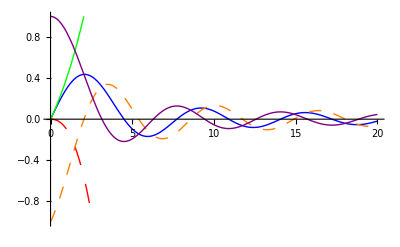

```mathematica
a=SphericalBesselJ[1,x];
b=Sum[x^n*2^n n^1/((2n+1)!),{n,0,500}];
c=Sum[1/x*Sin[x-n*Pi/2],{n,0,500}];
Plot[{a,a-b,a-c,b,c},{x,0,20},PlotRange->{-1,1},PlotStyle->{{Blue},{Red,Dashing[Large],Thick},{Orange,Dashing[Medium]},{Green},{Purple}},PlotLegend->{a,"small approx error","large approx error","small approx.","large approx."},LegendPosition->{.5,.18},LegendSize->{1.5,.7}]
```

### 12.20.18

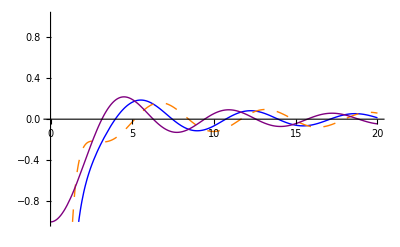

```mathematica
a1=SphericalBesselY[2,x];
b1= ∑_(n=0)^50 -(1 (2n)!)/(2^n n!x^(n+1)); 
c1=∑_(n=0)^50 -1/x Cos[x-n π/2];
Plot[{a1,a1-b1,a1-c1,b1,c1},{x,0,20},PlotRange->{-1,1},PlotStyle->{{Blue,Thick},{Red,Dashing[Large],Thick},{Orange,Dashing[Medium]},{Black, Dotted},{Purple}},PlotLegend->{a1,"small approx error","large approx error","small approx.","large approx."},LegendPosition->{.5,.18},LegendSize->{1.5,.7}]
```

Note on this problem the small argument aprroximation is really far off so it doesn’t even show up in the range specified in the hint. See below for an example of a few points between 0.1, 1.1 and you will understand! The first column is the value of x, second column is the approximation, the third column is the value of Y_2 and the last column is the difference between the two.

```mathematica
Table[{x,b1,SphericalBesselY[2,x],b1-SphericalBesselY[2,x]},{x,0.1,1.1,.25}]
```

(0.1 | -2.72815×10^129 | -3005.01 | -2.72815×10^129
0.35 | -4.89212×10^101 | -71.4423 | -4.89212×10^101
0.6 | -5.654×10^89 | -14.7928 | -5.654×10^89
0.85 | -1.09348×10^82 | -5.56707 | -1.09348×10^82
1.1 | -2.1343×10^76 | -2.81963 | -2.1343×10^76)

### 12.14.6

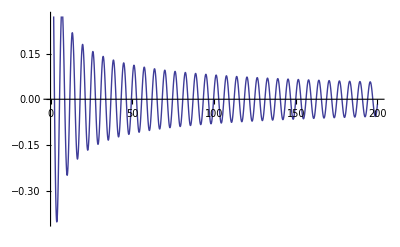

```mathematica
Plot[BesselJ[0,x],{x,0,200},GridLines->{{50Pi,51Pi},{}}]
```

7.4

### 12.5.1

```mathematica
Series[(1-y)^(-1/2),{y,0,4}]
```

1+y/2+(3 y^2)/8+(5 y^3)/16+(35 y^4)/128+O(y^5)

```mathematica
(2 x h  - h^2)^2//Expand
(2 x h  - h^2)^3//Expand
```

h^4-4 h^3 x+4 h^2 x^2

-h^6+6 h^5 x-12 h^4 x^2+8 h^3 x^3

7.5

### 12.6.6

```mathematica
D[LegendreP[0,x],x]*LegendreP[1,x]
D[LegendreP[n-1,x],x]*LegendreP[n,x]
```

0

(nx (n nx-n x n-1x))/(x^2-1)

7.6

### Additional Problem

```mathematica
partialSum[x_,N_]:=Sum[2/(BesselJ[5,BesselJZero[4,n]]*BesselJZero[4,n])*BesselJ[4,BesselJZero[4,n]*x],{n,1,N}];
```

```mathematica
plotFuncs = Table[partialSum[x,n],{n,1,5}]//N;
```

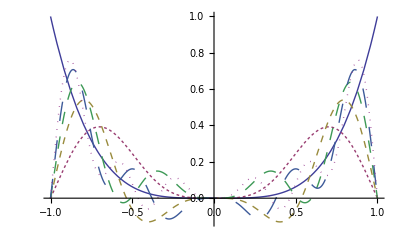

```mathematica
Plot[{x^4,plotFuncs},{x,-1,1},PlotStyle->{{Thick},{Dashing[Tiny]},{Dashing[Small]},{Dashing[Medium]},{Dashing[Large]},{Thick,Dotted}}]
```

7.7

### By hand

8.1

```mathematica
Manipulate[Plot[Sin[x(π+n/2)],{x,-3,3}],{n,1,5}]
```

8.3

### Additional Problem 1

8.4

### Additional Problem 2

```mathematica
p0 = 1; L = 1; Zl = 4*1.2*340; f1 = 500; k = 2 π f /340;c = 340;x2 = 1/3;
c1 = (-p0*Cos[k*L] - I*Zl*Sin[k L])/(Sin[k L] - I Zl/(p0 c)Cos[k L]); c2 = p0;
```

```mathematica
p1[x_] := c1*Sin[k*x]+c2*Cos[k*x]/.f->f1;
plotp1[x_] := Evaluate[Abs[p1[x]]^2]

p2[f_] := c1*Sin[k*x]+c2*Cos[k*x]/.x->x2;
plotp2[f_] := Evaluate[Abs[p2[f]]^2]
```

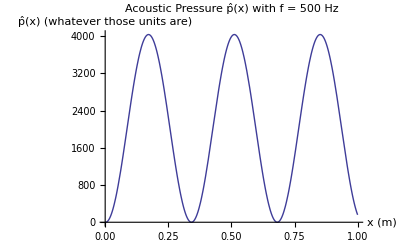

```mathematica
Plot[plotp1[x],{x,0,1},PlotLabel->"Acoustic Pressure p̂(x) with f = 500 Hz",AxesLabel->{"x (m)","p̂(x) (whatever those units are)"}]
```

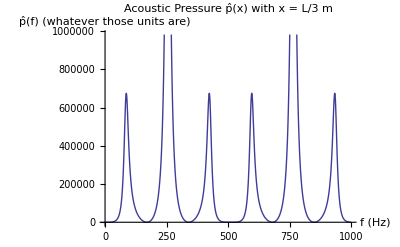

```mathematica
Plot[plotp2[x],{x,0,1000},PlotLabel->"Acoustic Pressure p̂(x) with x = L/3 m",AxesLabel->{"f (Hz)","p̂(f) (whatever those units are)"}]
```

8.6

### Additional Problem

```mathematica
an=1/((λ-n^2 π^2)*Nn2)Integrate[x*λ^(1/4)Sinc[√λ x],{x,0,1}]
```

-(4 λ^(1/4) (1-cos(√λ)))/((sin(2 √λ)-2 √λ) (λ-π^2 n^2))

```mathematica
Nn2=Integrate[x^2*(λ^(1/4)*Sinc[√λ x])^2,{x,0,1}]
```

-(sin(2 √λ)-2 √λ)/(4 λ)

```mathematica
an*λ^(1/4)*Sinc[√λ x]//FullSimplify
```

(4 √λ (cos(√λ)-1) sinc(√λ x))/((sin(2 √λ)-2 √λ) (λ-π^2 n^2))

Exam 2

### Problem 3

```mathematica
g[n_,x_]:=x^(-5/4)Exp[-x]Sin[n π (x/L)^(3/2)]
f[x_]:= x^(1/4)Exp[-x]
w[x_]:=x^3 Exp[2 x]
```

```mathematica
ncn = Assuming[n∈Integers&&L>0,Integrate[g[n,x]*w[x]*f[x],{x,0,L}]]
```

-(2 L^3 (-1)^Abs[n])/(3 π n)

```mathematica
nn = Assuming[n∈Integers&&L>0&&n≥0,Integrate[w[x]*g[n,x]^2,{x,0,L}]]
```

L^(3/2)/3

```mathematica
cn[n_]:=(2*L^(3/2)*(-1)^(n+1))/(n*π)
```

```mathematica
sum[n_]:=Sum[cn[i]*g[i,x],{i,1,n}]
```

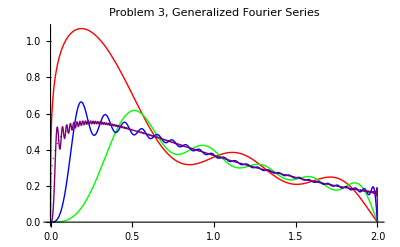

```mathematica
Plot[{sum[5]/.L->2,sum[10]/.L->2,sum[50]/.L->2,sum[500]/.L->2,f[x]/.L->2},{x,0,2},PlotStyle->{Red,Green,Blue,Purple,{Thick, Dotted,Black}},PlotLegend->{"n=5","n=10","n=50","n=500","f(x)"},LegendPosition->{.3,.15},PlotLabel->"Problem 3, Generalized Fourier Series"]
```

### Problem 4

```mathematica
s = 1; y = 1;  L =15; m =2; w=1; s0 =1;
```

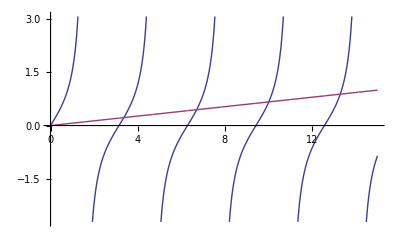

```mathematica
Plot[{Tan[x],x*((s*y)/(L*m*w^2-L*s0))},{x,0,L},Exclusions->Range[0,L,π/2]]
```

```mathematica
eigenfunc = (1-(2*α^2)/(2*15^2))*Sin[α*x/15]+Cos[α*x/15];
```

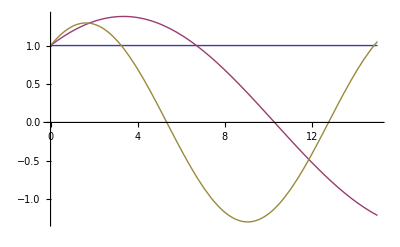

```mathematica
Plot[{eigenfunc/.α->0,eigenfunc/.α->3.4,eigenfunc/.α->6.35},{x,0,15}]
```

### Problem 5

#### a.)

```mathematica
f[x_]:=Exp[-x]*x^(9/2)
w[x_]:=Exp[-2 x]*x^7
ψ[x_,n_]:=x^(-5/2)*Exp[x]*Sin[n π x^3]
```

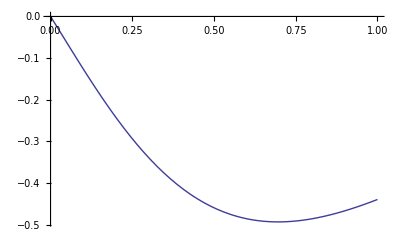

```mathematica
Plot[Exp[-2 x]*(x^3-3 x^2 - 5/4 x),{x,0,1}]
```

```mathematica
nn = Assuming[n∈Integers,Integrate[w[x]*ψ[x,n]^2,{x,0,1}]]
an = Assuming[n∈Integers,1/((λ-9(n π)^2)*nn)*Integrate[f[x]*ψ[x,n],{x,0,1}]]
```

1/6

-(2 ((-1)^n-1))/(π n (λ-9 π^2 n^2))

```mathematica
Integrate[f[x]*ψ[x,n],{x,0,1}]
```

-(cos(π n)-1)/(3 π n)

```mathematica
f[x]*ψ[x,n]
```

x^2 sin(π n x^3)

```mathematica
.10
```

9.1

```mathematica
x
```

9.2

### Boas 13.2.1

```mathematica
lx = 10; ymax = 10; T[x_,y_,nn_]:=20/π Sum[(-1)^(n+1)/n Exp[-n π y /10]*Sin[n π x/10],{n,1,nn}];nn = {1,2,5,10,100,500};
```

```mathematica
plotn[n_]:=ShowLegend[DensityPlot[T[x,y,n],{x,0,10},{y,0,10},ColorFunction->"TemperatureMap",PlotPoints->50,PlotLabel->"n="<>ToString[n],PlotRange->{0,10}],{ColorData["TemperatureMap"][1-#1]&,10," hot","cold",LegendPosition->{1.1,-.4}}]
```

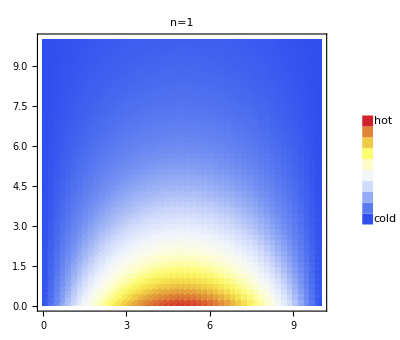
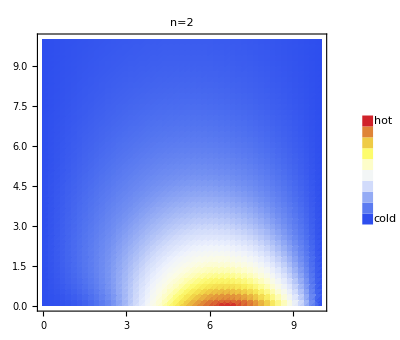
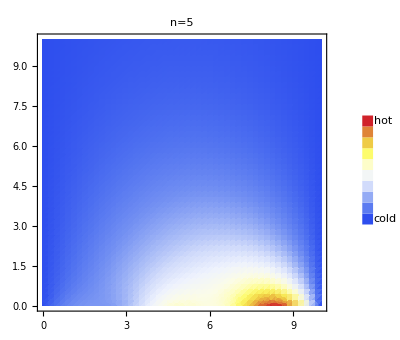
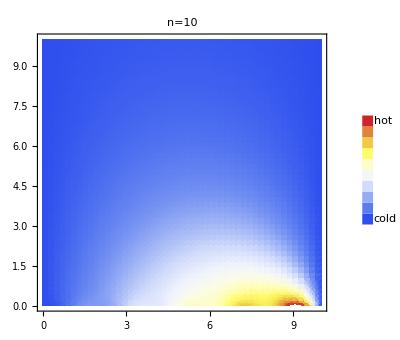
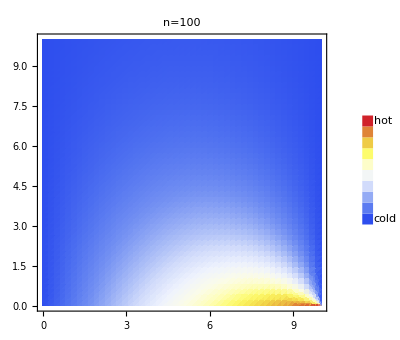
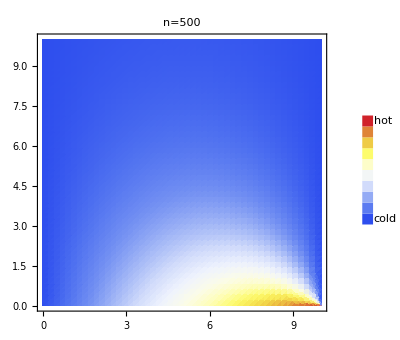

```mathematica
plotn[#]&/@nn
```

It is easy to see that these plots look pretty similar. As we add more terms the edges get less sharp and we get a smooth temperature distribution.

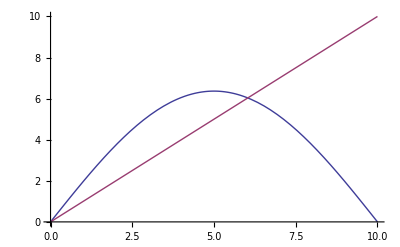
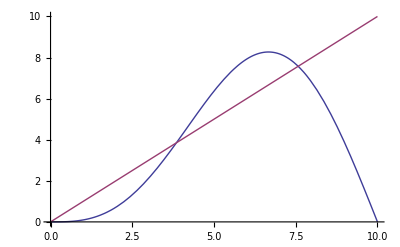
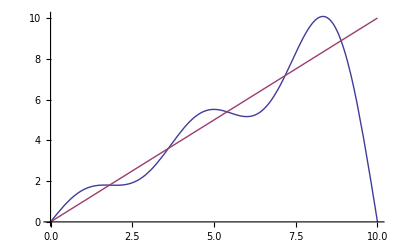
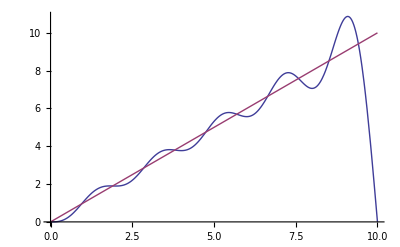
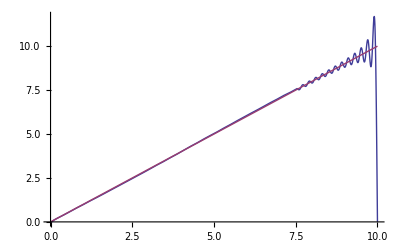
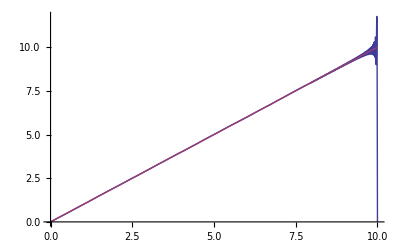

```mathematica
Table[Plot[{T[x,0,nn[[i]]],x},{x,0,10},PlotLegend->{StringJoin["n=",ToString[nn[[i]]]],"f(x)=x"}],{i,1,Length[nn]}]
```

In these plots we can clearly see that progressively going from n=1 to n=500 makes our approximations of f(x)=x much more accurate. 
We could tell that we have enough terms by looking at terms of the summation specific to values of n. Because of the negative exponential each term wil be smaller in magnitude than the term preceeding it. If we look at one term at a time and pick a certain threshold for how big we want the marginal term to be we can find what value of n gives us that number. A quick example of this decreasing bahavior in n is below with x=1, y=1, and n = {1,2,...,10}

```mathematica
Table[{i,T[1,1,i]},{i,1,10}]//N
```

(1. | 1.43689
2. | 0.43875
3. | 1.10771
4. | 0.676915
5. | 0.941595
6. | 0.788377
7. | 0.869975
8. | 0.832086
9. | 0.845019
10. | 0.845019)

9.3

### 13.2.12

```mathematica
a213[n_]:=-200/(n π Sinh[3 n π])*((-1)^n-1); c213[n_]:=-200/(n π Sinh[n π/3])*((-1)^n-1)
T213[x_,y_,nn_]:=Sum[ a213[n]*Sin[n π x/10]*Sinh[n π (30-y)/10],{n,1,nn}]+Sum[ c213[n]*Sin[n π y/30]*Sinh[n π (10-x)/30],{n,1,nn}];nn= {1,2,5,10,35,100};
```

```mathematica
plotn[n_]:=ShowLegend[DensityPlot[T213[x,y,n],{x,0,10},{y,0,30},ColorFunction->"TemperatureMap",PlotPoints->50,PlotLabel->"n="<>ToString[n],PlotRange->Automatic,AspectRatio->Automatic],{ColorData["TemperatureMap"][1-#1]&,10," hot","cold",LegendPosition->{.5,-.4}}]
```

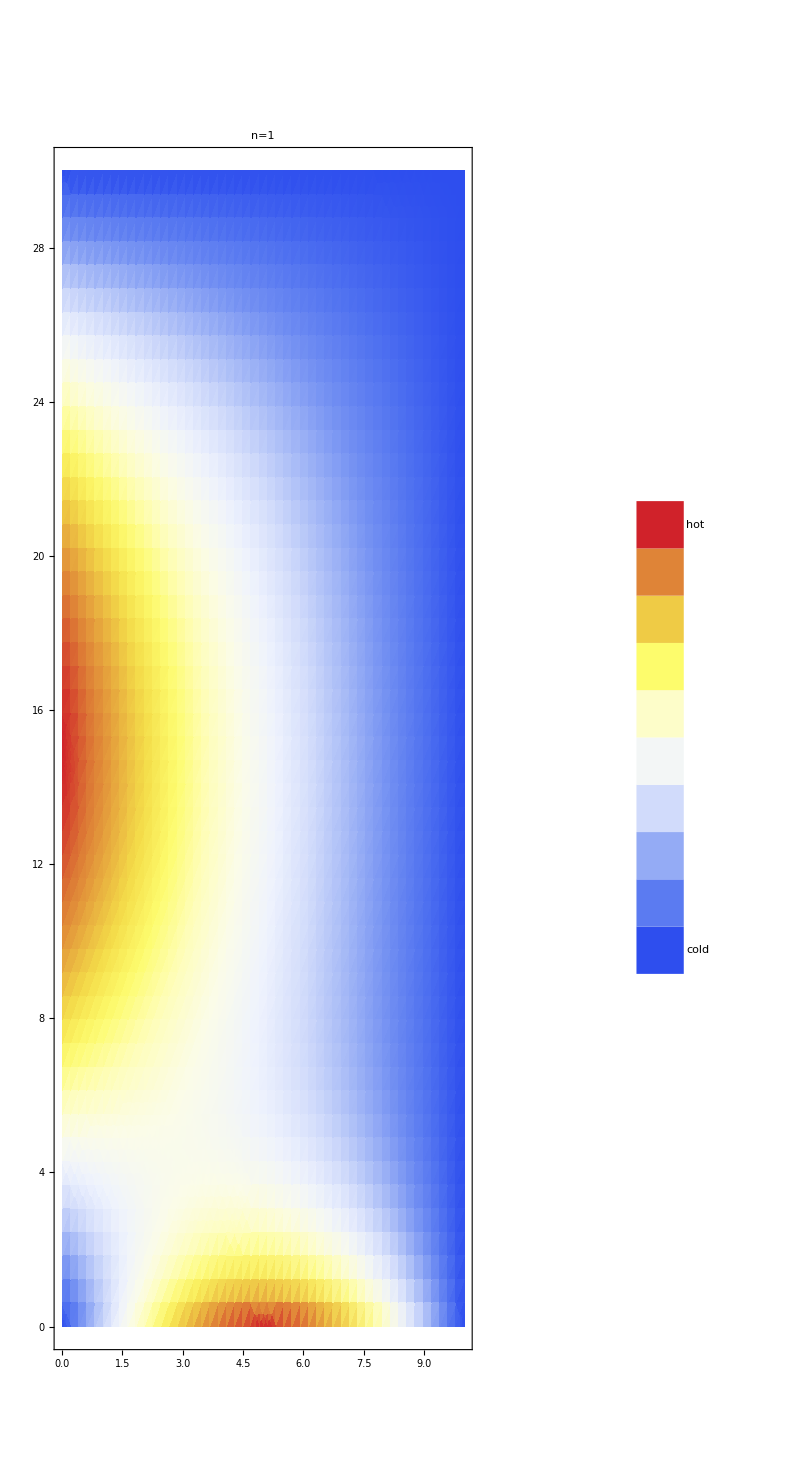
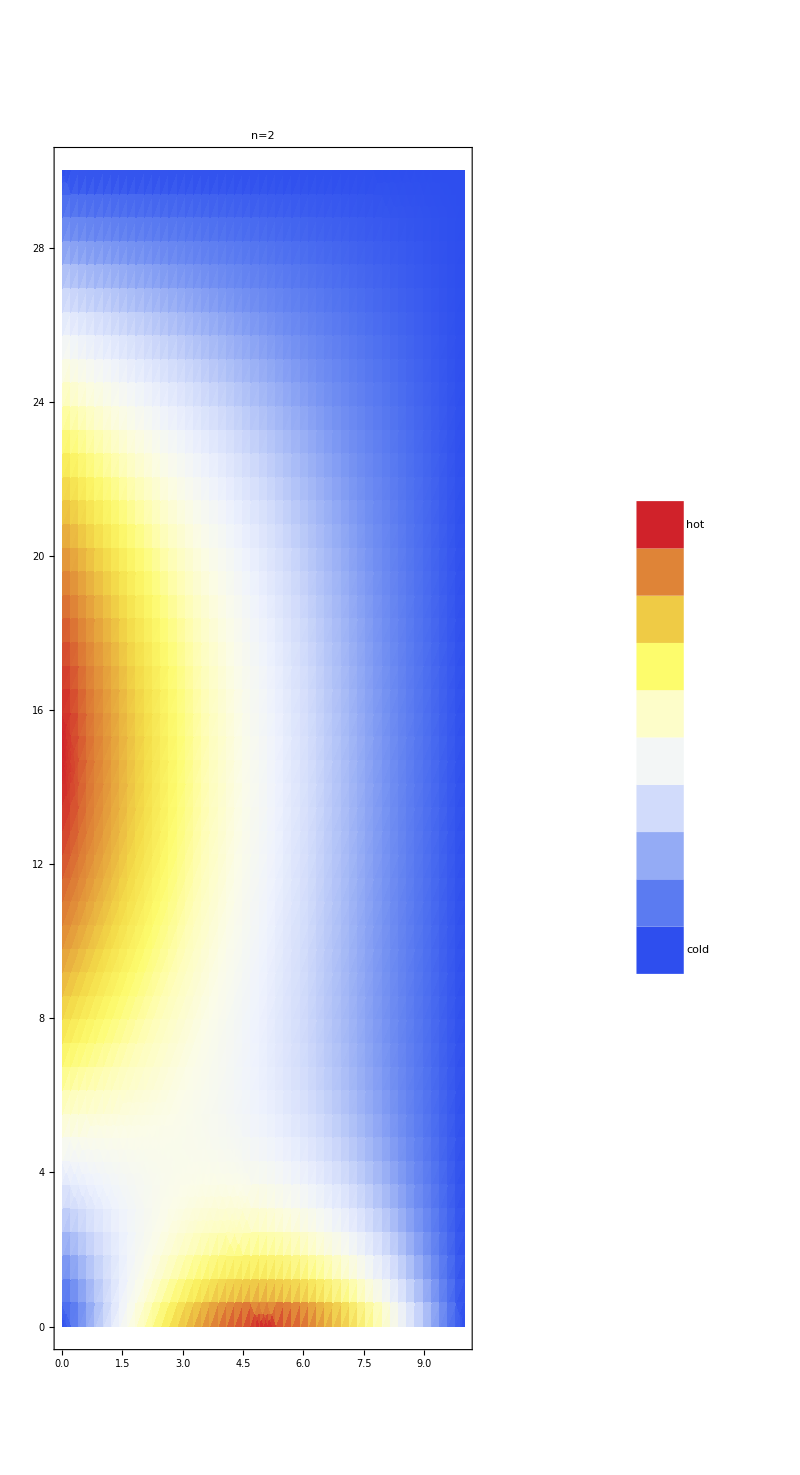
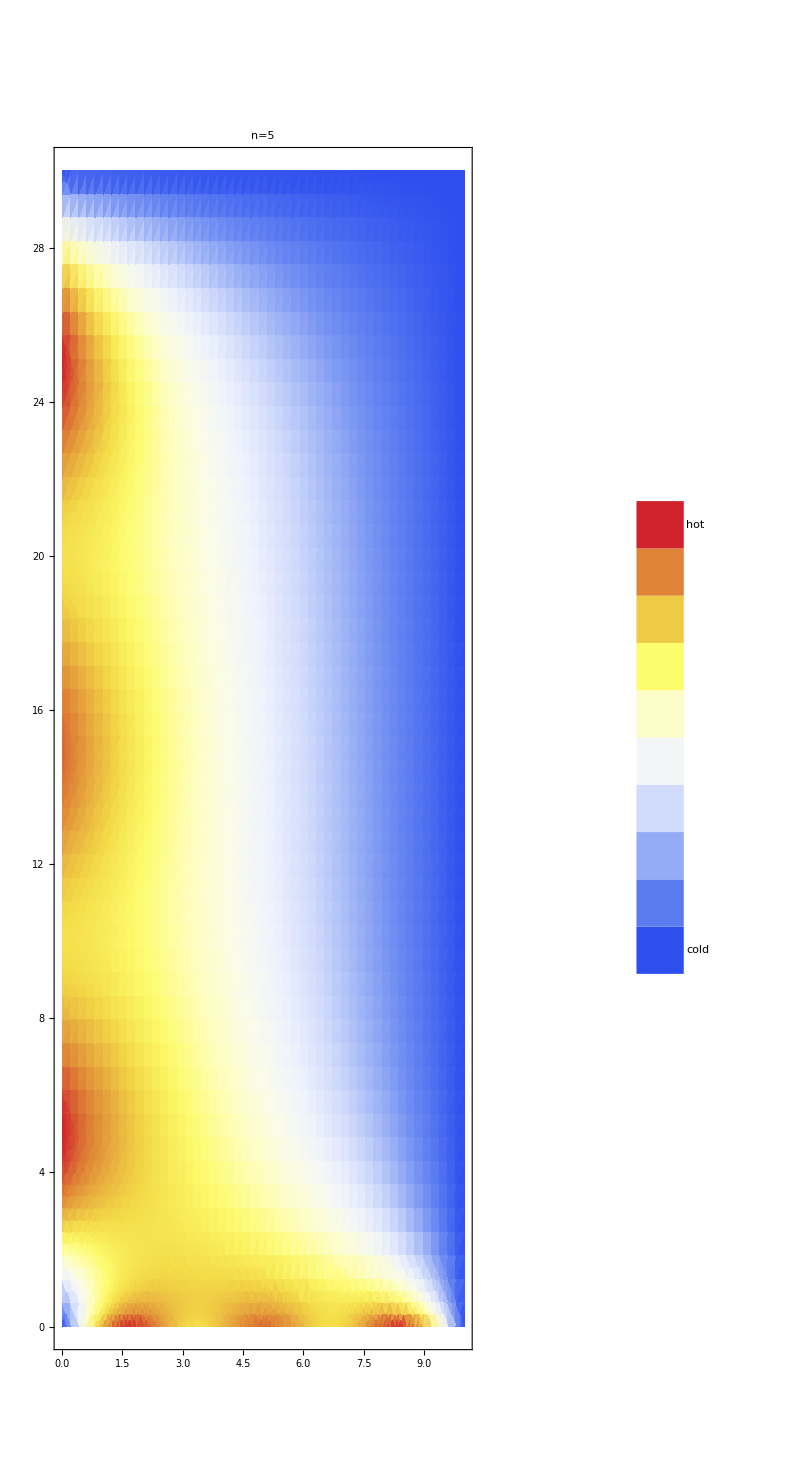
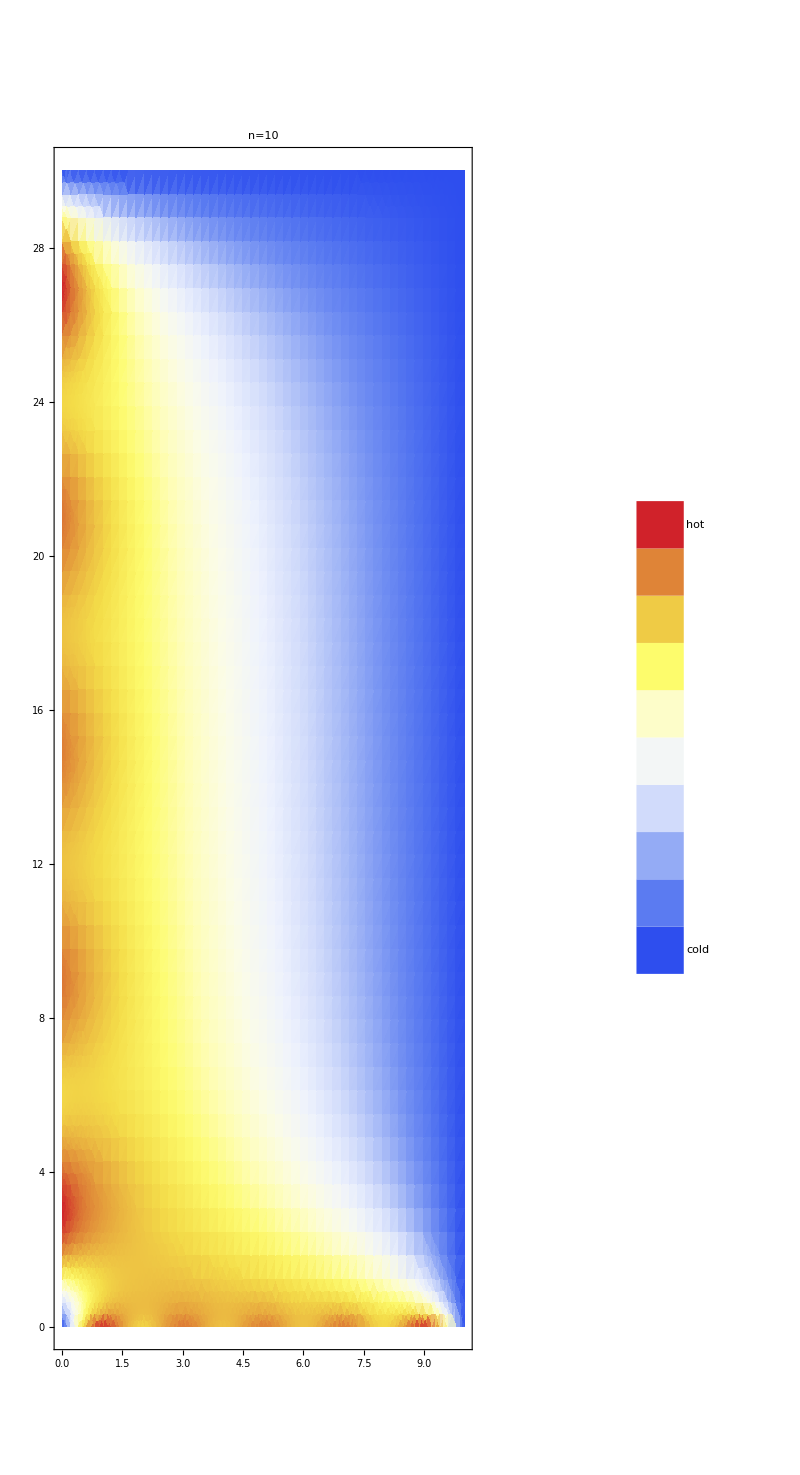
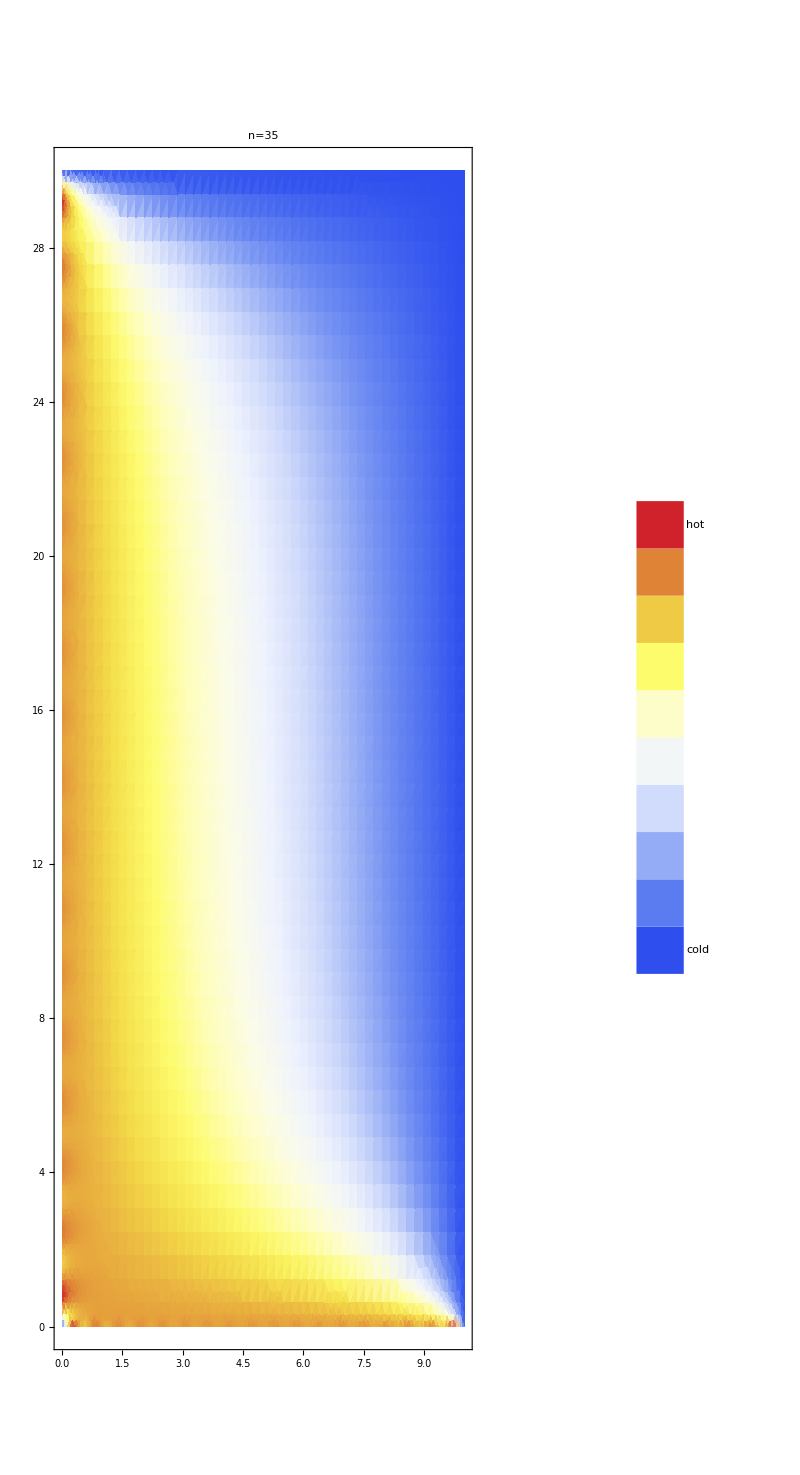
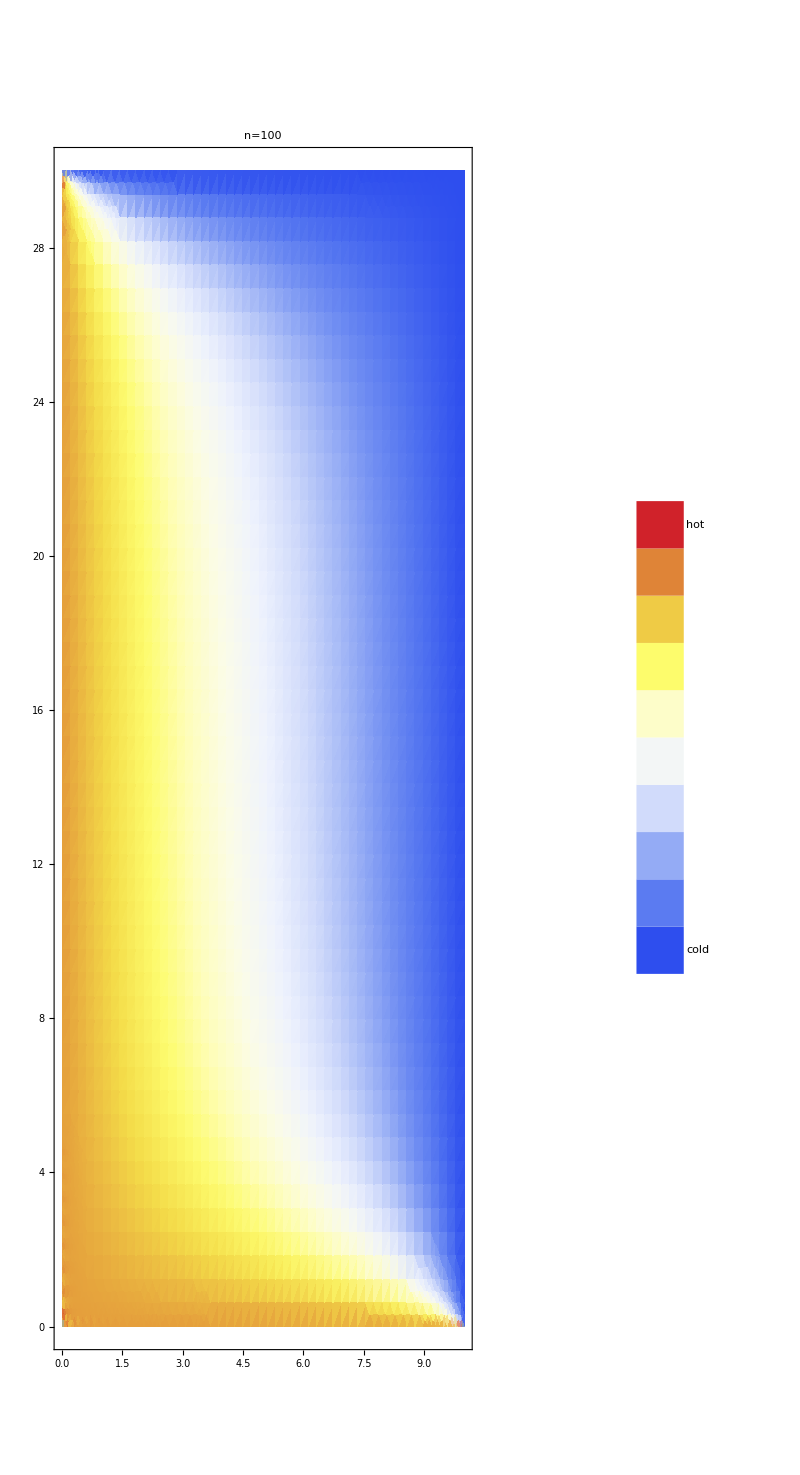

```mathematica
plotn[#]&/@nn
```

9.4

```mathematica
T14x[x_,y_,nn_]:=1/6(30-y) - 40/π^2 Sum[1/(n^2 Sinh[3 π n])Sinh[(n π)/10(30-y)]Cos[n π x/10],{n,1,nn,2}];
T94100[x_,y_,nn_]:=10/3(30-y); nn94 = {1,2,5,10,35,100};
```

```mathematica
plotn94x[n_]:=ShowLegend[DensityPlot[T14x[x,y,n],{x,0,10},{y,0,30},ColorFunction->"TemperatureMap",PlotPoints->50,PlotLabel->"n="<>ToString[n],PlotRange->Automatic,AspectRatio->Automatic],{ColorData["TemperatureMap"][1-#1]&,10," hot","cold",LegendPosition->{.5,-.4}}]
plotn94100[n_]:=ShowLegend[DensityPlot[T94100[x,y,n],{x,0,10},{y,0,30},ColorFunction->"TemperatureMap",PlotPoints->50,PlotLabel->"n="<>ToString[n],PlotRange->Automatic,AspectRatio->Automatic],{ColorData["TemperatureMap"][1-#1]&,10," hot","cold",LegendPosition->{.5,-.4}}]
```

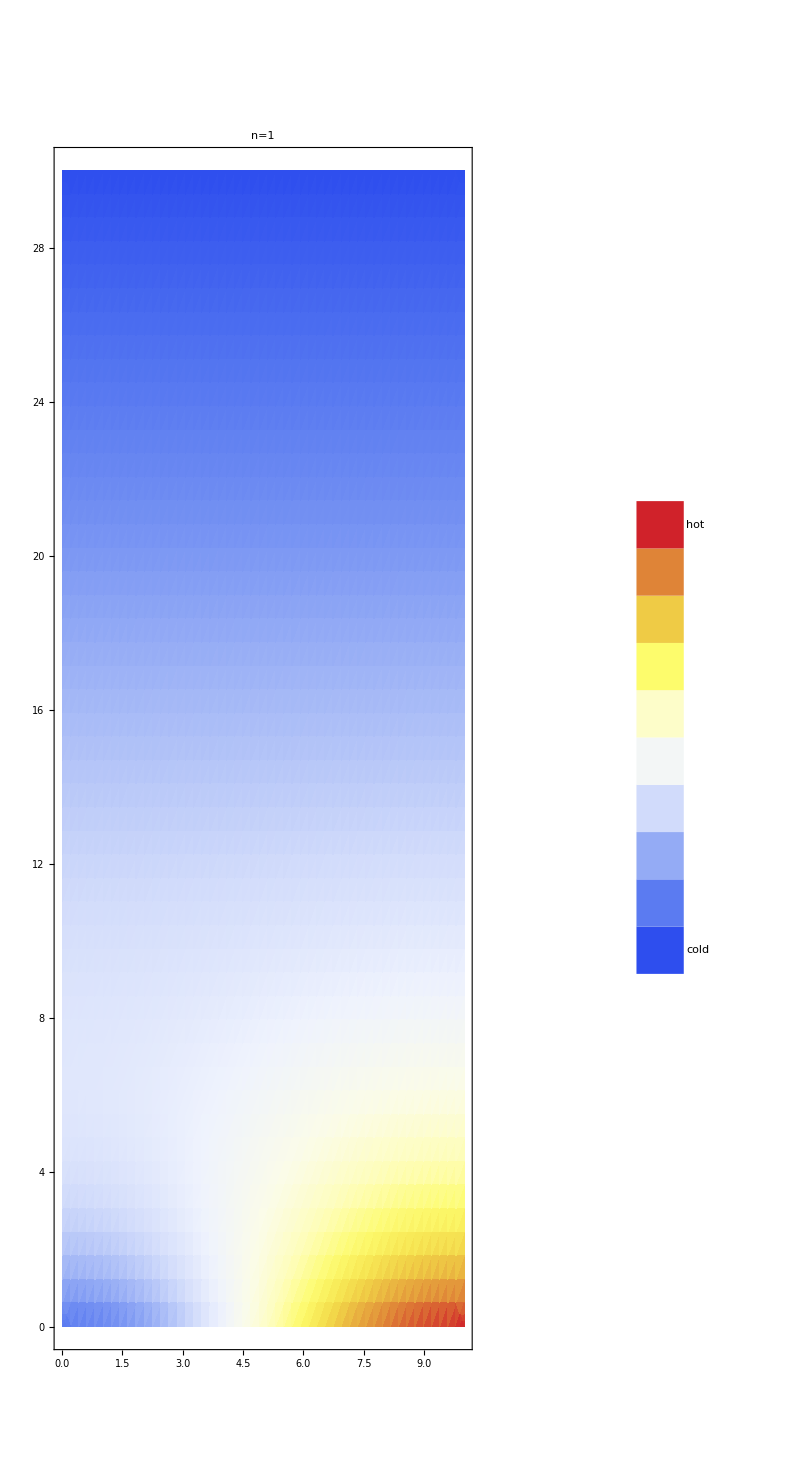
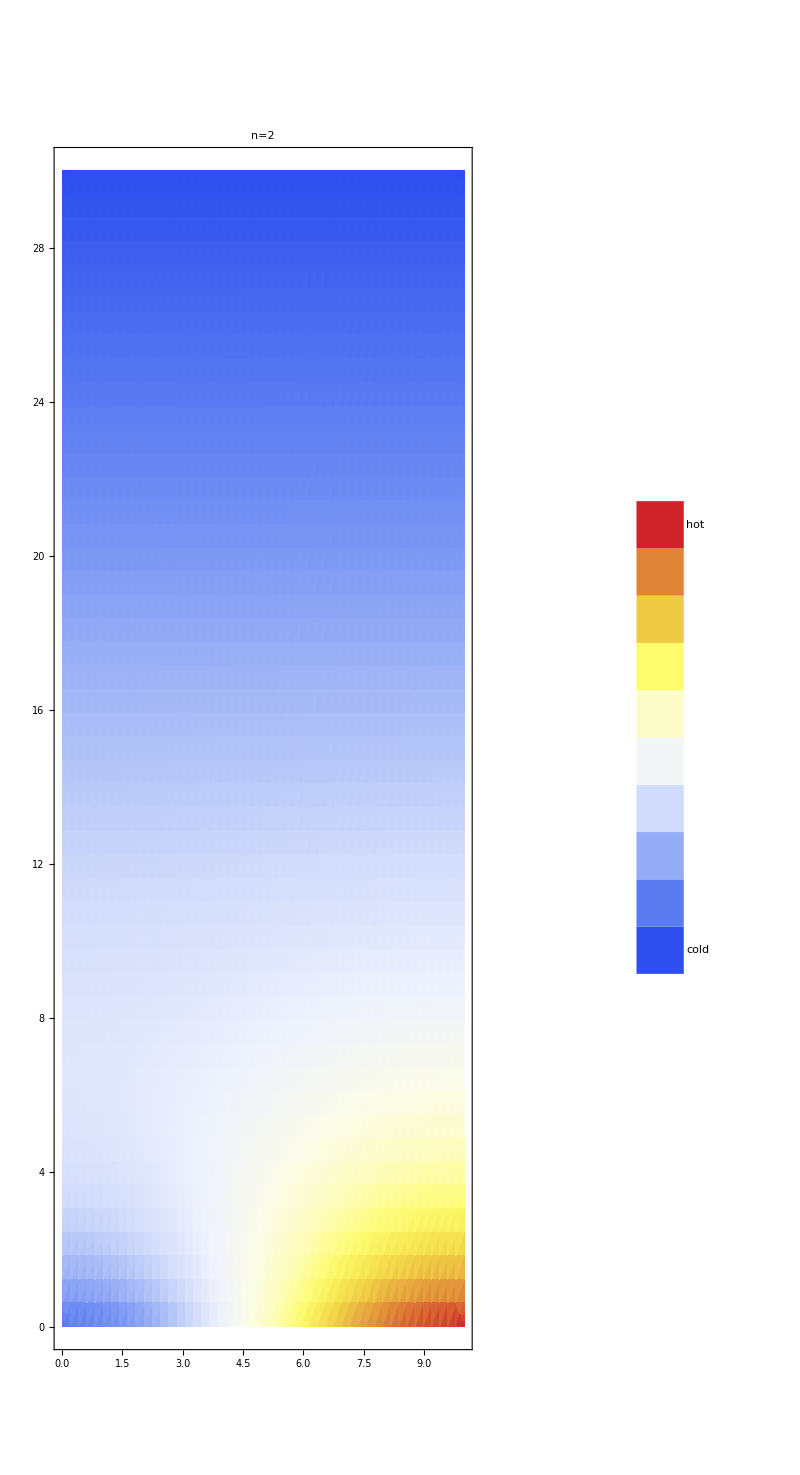
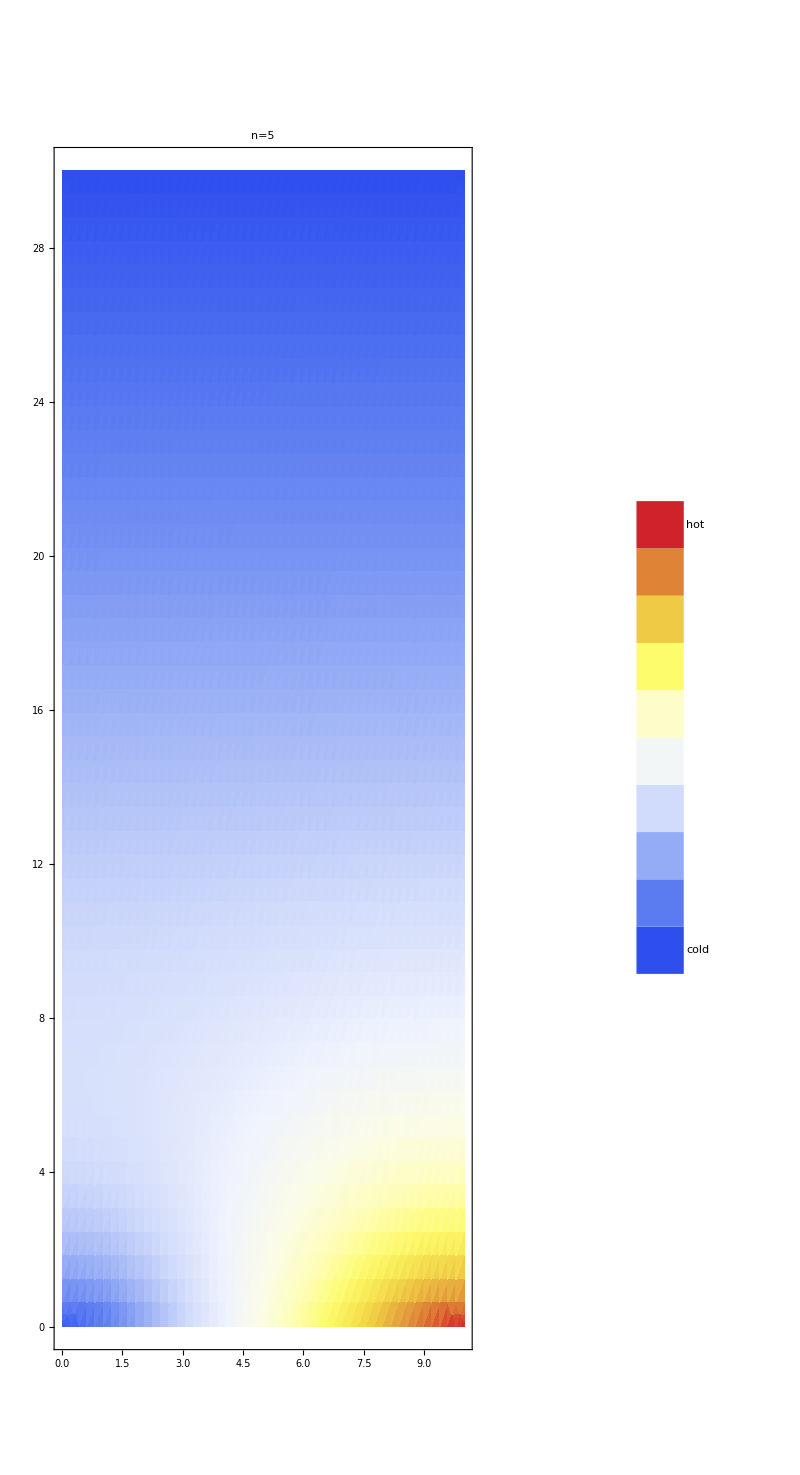
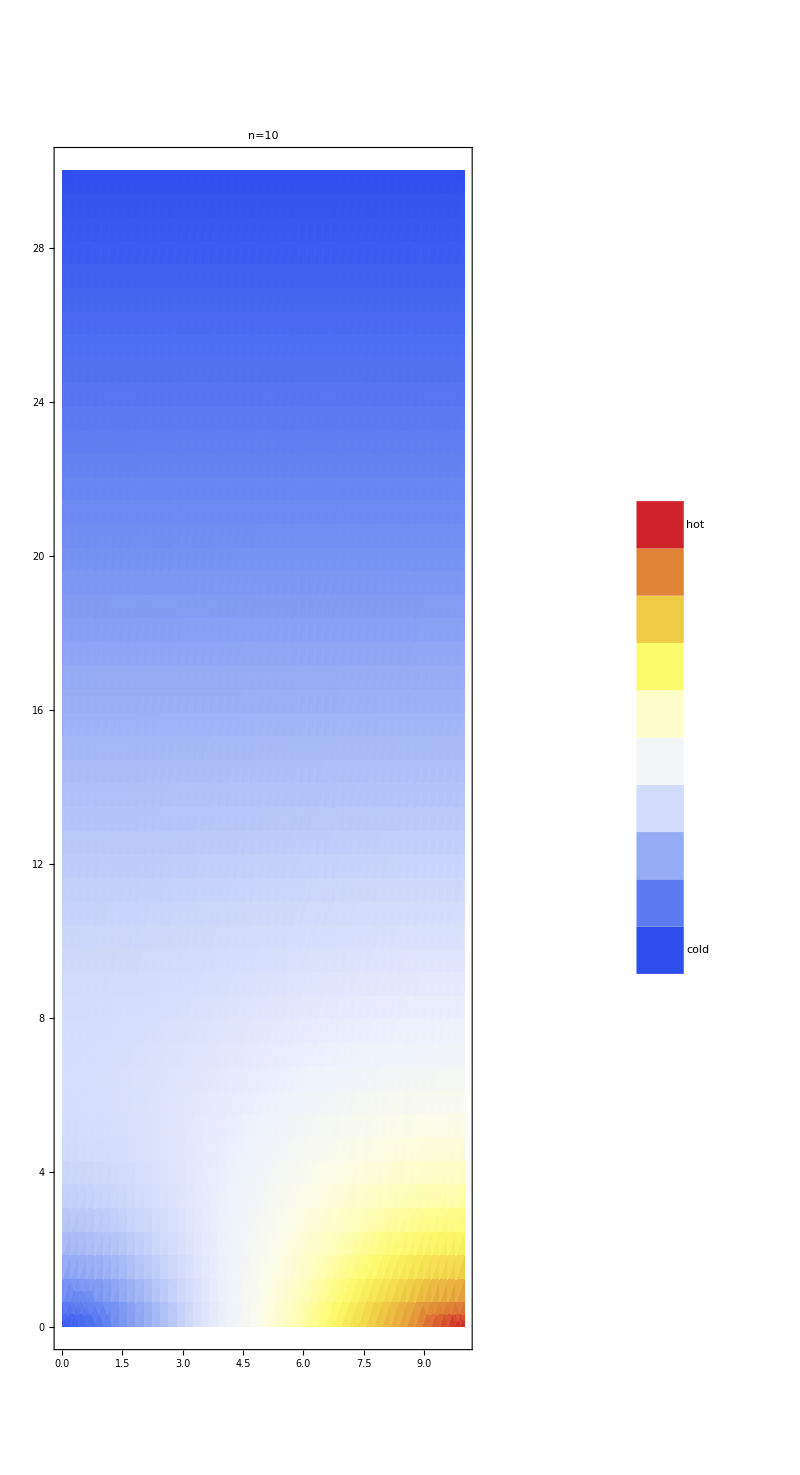
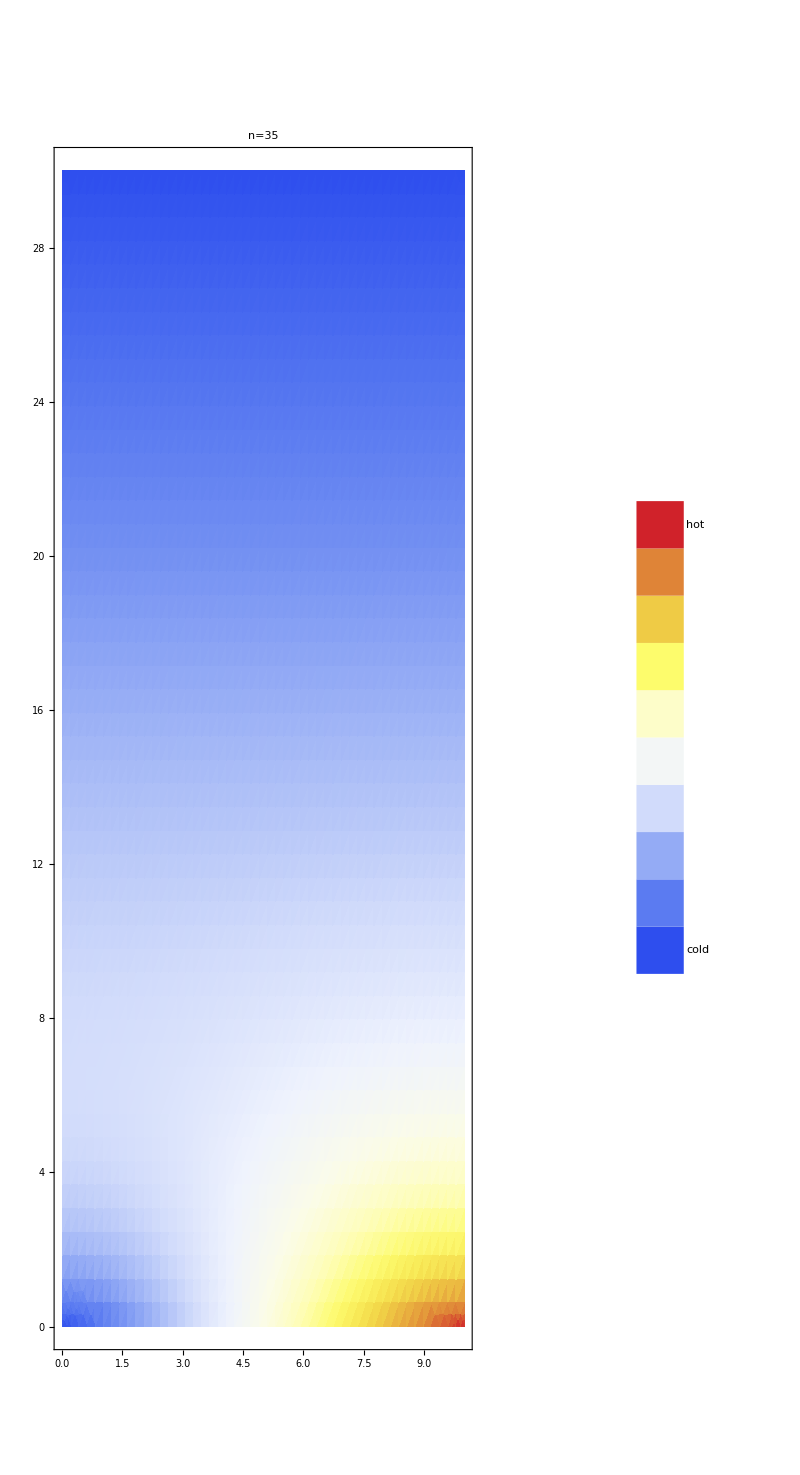
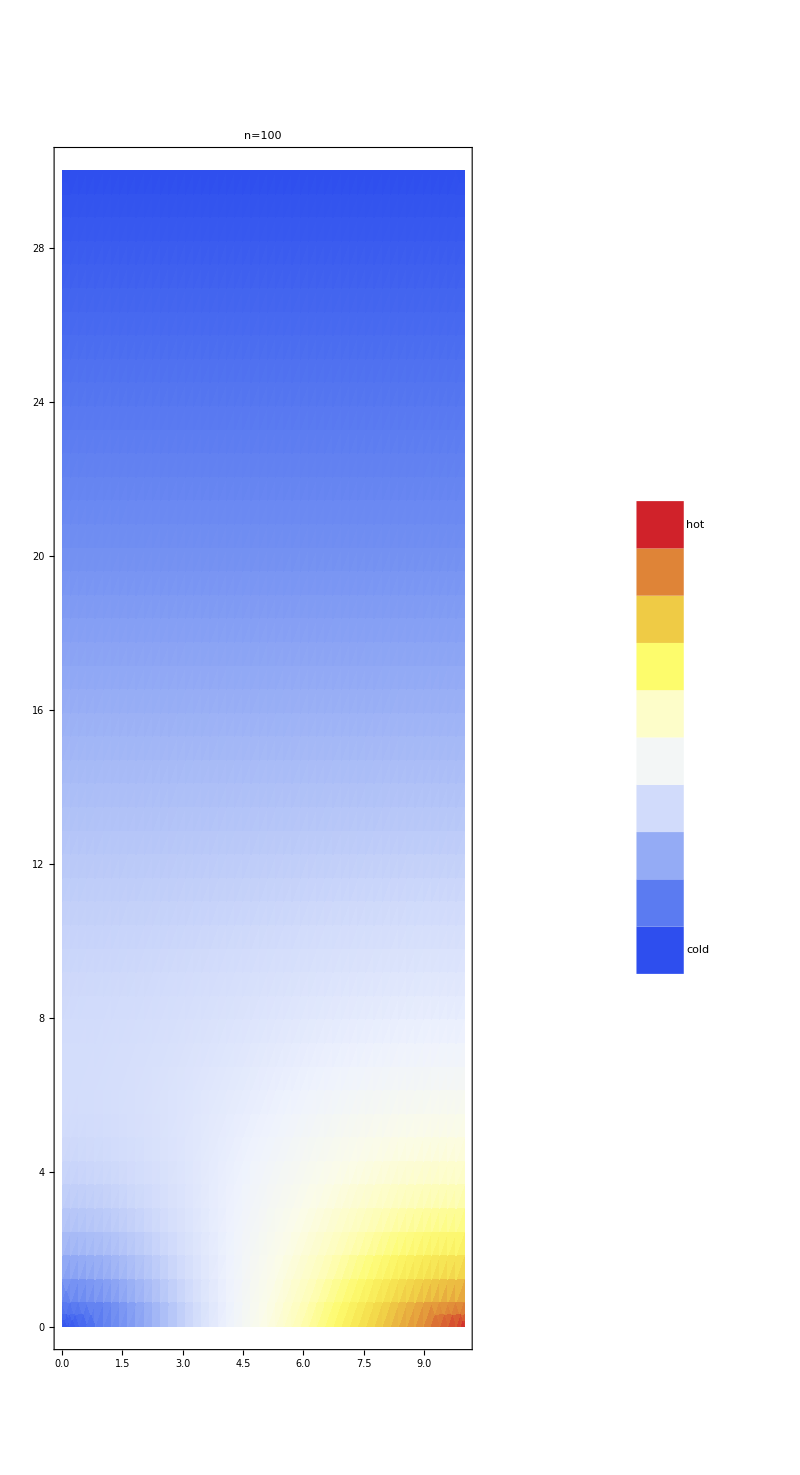

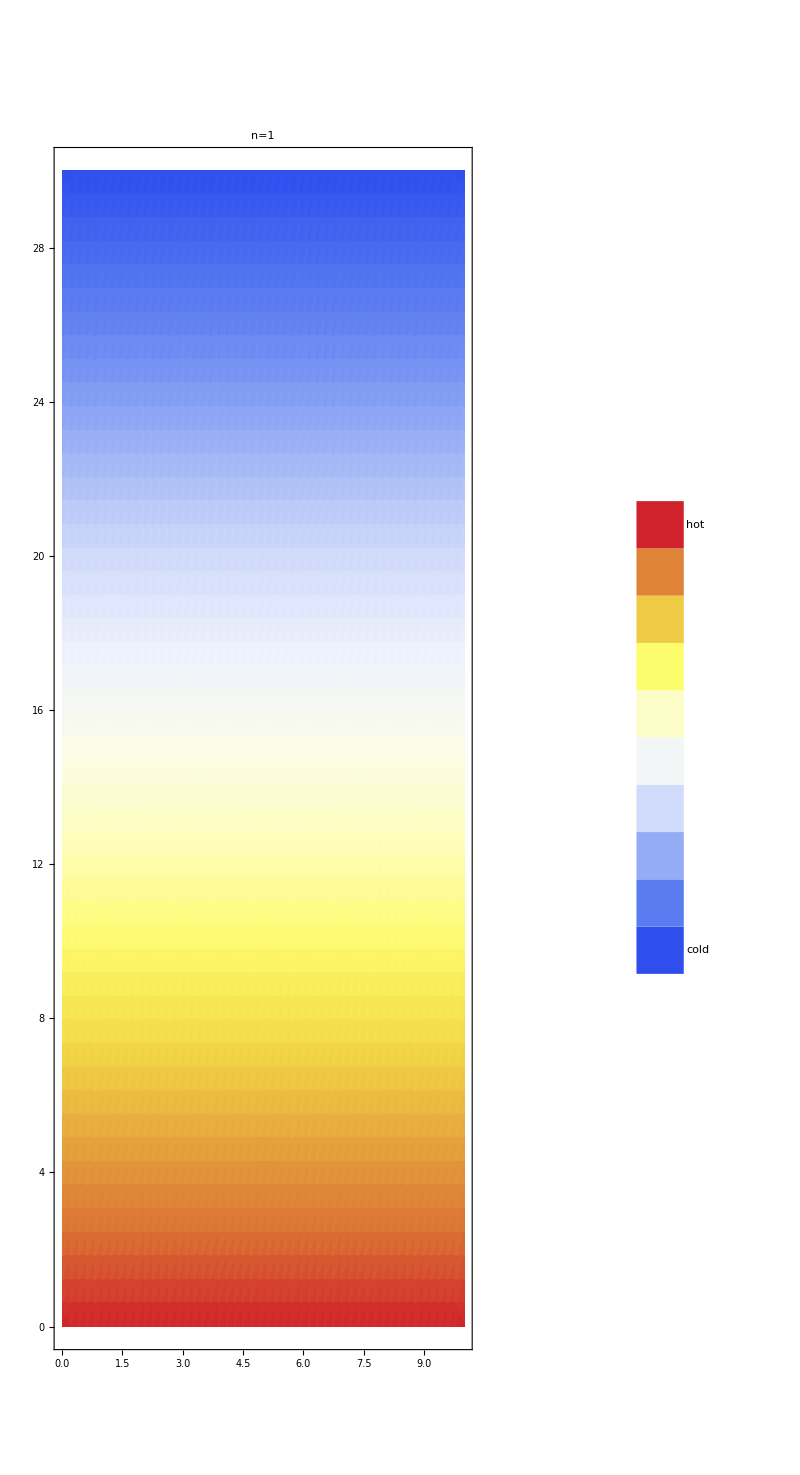
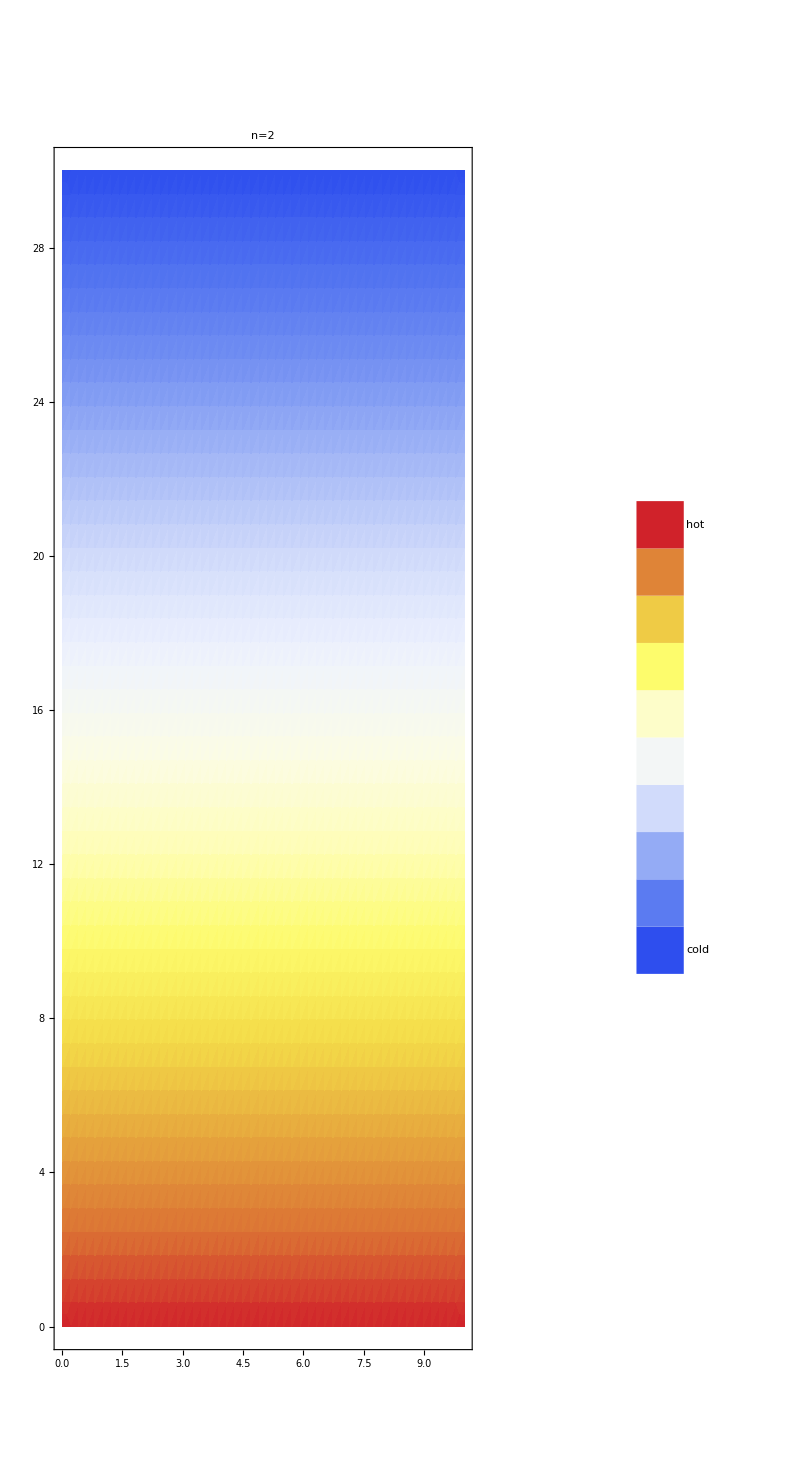

```mathematica
plotn94x[#]&/@nn94
plotn94100[#]&/@nn94
```

9.5

### Additional Problem

```mathematica
T95[x_,y_,nn_]:=Sum[16/(π^2(n^2 π^2+m^2 π^2+3)m*n)Sin[m π x]*Sin[n π y],{n,1,nn,2},{m,1,nn,2}] ;ns = {1,2,5,10,35,100};
```

```mathematica
plotn[n_]:=ShowLegend[DensityPlot[T95[x,y,n],{x,0,1},{y,0,1},ColorFunction->"BlueGreenYellow",PlotPoints->15,PlotLabel->"n="<>ToString[n],PlotRange->Automatic,AspectRatio->Automatic],{ColorData["BlueGreenYellow"][1-#1]&,10," hot","cold",LegendPosition->{.5,-.4}}]
```

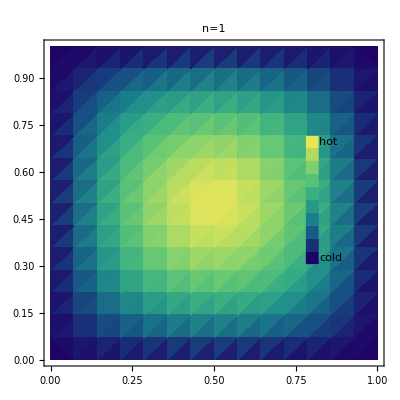
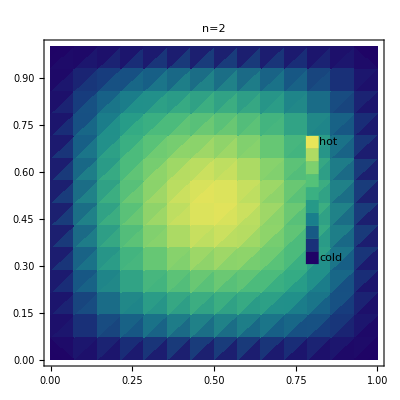
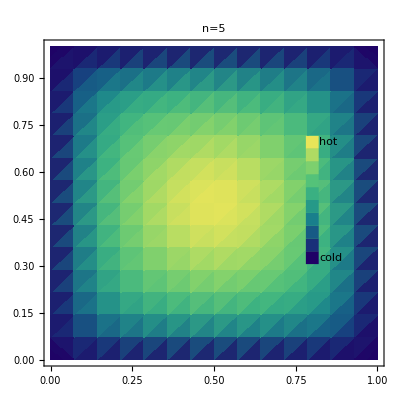
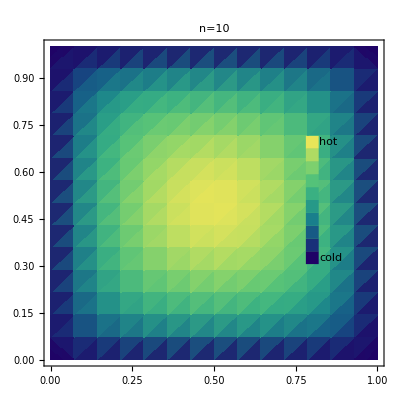
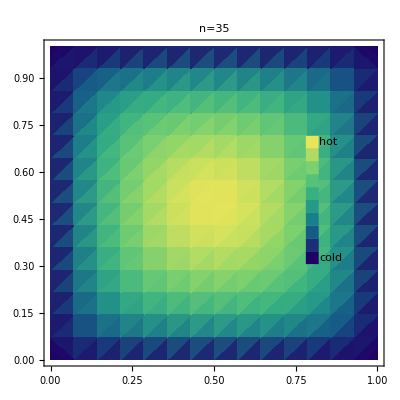
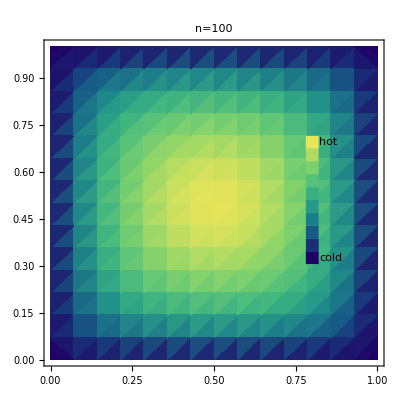

```mathematica
plotn[#]&/@ns
```

9.6

### Boas 13.4.3

```mathematica
L = 1; c = 100; h = 0.05;
```

```mathematica
Assuming[n∈Integers&&n>0,2/L*(Integrate[Sin[(n π x)/L]*8h x/L,{x,0,L/8}]+Integrate[(2h - 8h x/L)*Sin[n x π/L],{x,L/8,L/4}])]//FullSimplify//Chop//InputForm
```

(64*h*Sin[(n*Pi)/16]^2*Sin[(n*Pi)/8])/(n^2*Pi^2)

```mathematica
y2[x_,t_,nn_]:=Sum[((0.16211389382774044*Sin[(n*Pi)/8]-0.08105694691387022*Sin[(n*Pi)/4])/n^2)*Sin[n π x/L]*Cos[n π c t/L],{n,1,nn}]
```

```mathematica
y2[x_,t_,nn_]:=(16h)/π^2 Sum[1/n^2(2Sin[n π /8]-Sin[n π/4])*Sin[n π x/L]*Cos[(n π)/L c *t],{n,1,nn}]
```

```mathematica
SetDirectory["/Users/spencerlyon2/Desktop"]
```

/Users/spencerlyon2/Desktop

```mathematica
export3 = Table[Plot[y2[x,t,200],{x,0,L},PlotRange->{-.05,.05}],{t,0,.02,.001}];
Export["SpencerLyonBoas1343.avi",export3]
```

SpencerLyonBoas1343.avi

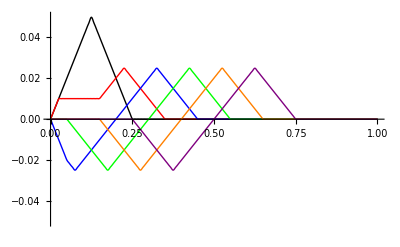

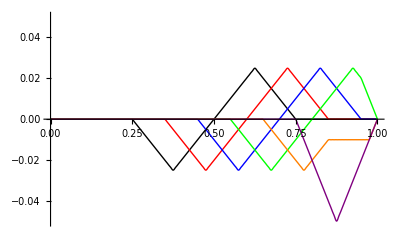

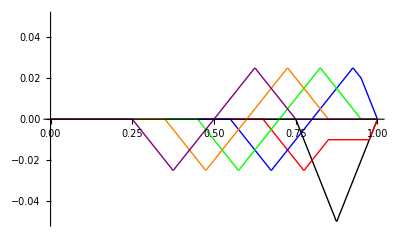

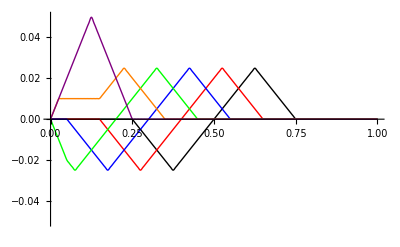

```mathematica
Plot[{y2[x,0,200],y2[x,0.001,200],y2[x,0.002,200],y2[x,0.003,200],y2[x,0.004,200],y2[x,0.005,200]},{x,0,L},PlotStyle->{{Black,Thick},{Red},{Blue},{Green},{Orange},{Purple}},PlotLegend->{"t=0 ms","t=1 ms","t=2 ms","t=3 ms","t=4 ms","t=5 ms"},PlotRange->{-0.05,0.05}]
Plot[{y2[x,0.005,200],y2[x,0.006,200],y2[x,0.007,200],y2[x,0.008,200],y2[x,0.009,200],y2[x,0.01,200]},{x,0,L},PlotStyle->{{Black,Thick},{Red},{Blue},{Green},{Orange},{Purple}},PlotLegend->{"t=5 ms","t=6 ms","t=7 ms","t=8 ms","t=9 ms","t=10 ms"},PlotRange->{-0.05,0.05}]
Plot[{y2[x,0.01,200],y2[x,0.011,200],y2[x,0.012,200],y2[x,0.013,200],y2[x,0.014,200],y2[x,0.015,200]},{x,0,L},PlotStyle->{{Black,Thick},{Red},{Blue},{Green},{Orange},{Purple}},PlotLegend->{"t=10 ms","t=11 ms","t=12 ms","t=13 ms","t=14 ms","t=15 ms"},PlotRange->{-0.05,0.05}]
Plot[{y2[x,0.015,200],y2[x,0.016,200],y2[x,0.017,200],y2[x,0.018,200],y2[x,0.019,200],y2[x,0.02,200]},{x,0,L},PlotStyle->{{Black,Thick},{Red},{Blue},{Green},{Orange},{Purple}},PlotLegend->{"t=15 ms","t=16 ms","t=17 ms","t=18 ms","t=19 ms","t=20 ms"},PlotRange->{-0.05,0.05}]
```

### Boas 13.4.6

```mathematica
h = 2; w=0.1;L=1;c=100;
```

```mathematica
const =2/L Integrate[h*Sin[(n π x)/L],{x,L/2-w,L/2+w}];
goodconst = const*L/(n π c);
```

```mathematica
y3[x_,t_,nn_]:=4/π Sum[1/n(Cos[(n π)/L(L/2-w)] - Cos[(n π)/L(L/2+w)])*Sin[(n π)/L x]*Sin[(n π)/L c t],{n,1,nn}]
```

```mathematica
y3[x_,t_,nn_]:=Sum[goodconst*Sin[(n π)/L x]*Sin[(n π c)/L t],{n,1,nn}]
```

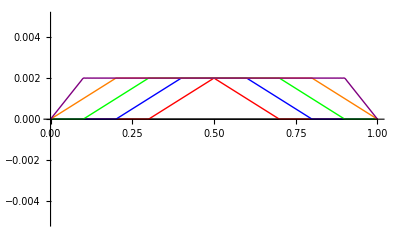

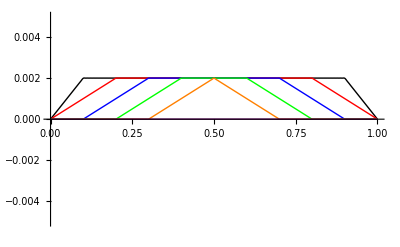

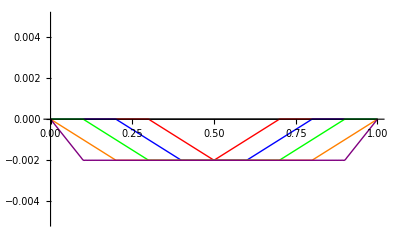

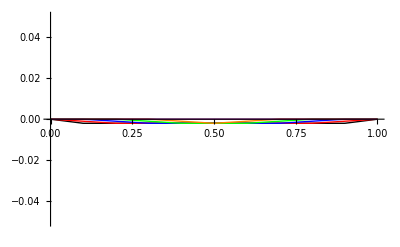

```mathematica
Plot[{y3[x,0,200],y3[x,0.001,200],y3[x,0.002,200],y3[x,0.003,200],y3[x,0.004,200],y3[x,0.005,200]},{x,0,L},PlotStyle->{{Black,Thick},{Red},{Blue},{Green},{Orange},{Purple}},PlotLegend->{"t=0 ms","t=1 ms","t=2 ms","t=3 ms","t=4 ms","t=5 ms"},PlotRange->{-0.005,0.005}]
Plot[{y3[x,0.005,200],y3[x,0.006,200],y3[x,0.007,200],y3[x,0.008,200],y3[x,0.009,200],y3[x,0.01,200]},{x,0,L},PlotStyle->{{Black,Thick},{Red},{Blue},{Green},{Orange},{Purple}},PlotLegend->{"t=5 ms","t=6 ms","t=7 ms","t=8 ms","t=9 ms","t=10 ms"},PlotRange->{-0.005,0.005}]
Plot[{y3[x,0.01,200],y3[x,0.011,200],y3[x,0.012,200],y3[x,0.013,200],y3[x,0.014,200],y3[x,0.015,200]},{x,0,L},PlotStyle->{{Black,Thick},{Red},{Blue},{Green},{Orange},{Purple}},PlotLegend->{"t=10 ms","t=11 ms","t=12 ms","t=13 ms","t=14 ms","t=15 ms"},PlotRange->{-0.005,0.005}]
Plot[{y3[x,0.015,200],y3[x,0.016,200],y3[x,0.017,200],y3[x,0.018,200],y3[x,0.019,200],y3[x,0.02,200]},{x,0,L},PlotStyle->{{Black,Thick},{Red},{Blue},{Green},{Orange},{Purple}},PlotLegend->{"t=15 ms","t=16 ms","t=17 ms","t=18 ms","t=19 ms","t=20 ms"},PlotRange->{-0.05,0.05}]
```

```mathematica
export6 = Table[Plot[y2[x,t,200],{x,0,L},PlotRange->{-.005,.005}],{t,0,0.02,0.001}];
```

```mathematica
Export["SpencerLyonBoas1346.avi",export6]
```

SpencerLyonBoas1346.avi

9.7

### Additional 1

#### c.)

```mathematica
Lx = 5; Ly = 6; Lz = 3.5;
```

```mathematica
naturalFrequencies = Table[{{l,n,m},1500/2 √((l/Lx)^2+(n/Ly)^2+ ((m+1/2)/Lz)^2)},{l,0,2},{m,0,2},{n,0,2}]
```

(({0,0,0} | 107.143
{0,1,0} | 164.635
{0,2,0} | 271.992) | ({0,0,1} | 321.429
{0,1,1} | 344.879
{0,2,1} | 407.206) | ({0,0,2} | 535.714
{0,1,2} | 550.104
{0,2,2} | 591.177)
({1,0,0} | 184.336
{1,1,0} | 222.721
{1,2,0} | 310.612) | ({1,0,1} | 354.706
{1,1,1} | 376.087
{1,2,1} | 433.954) | ({1,0,2} | 556.318
{1,1,2} | 570.188
{1,2,2} | 609.91)
({2,0,0} | 318.559
{2,1,0} | 342.205
{2,2,0} | 404.944) | ({2,0,1} | 439.678
{2,1,1} | 457.101
{2,2,1} | 505.783) | ({2,0,2} | 613.995
{2,1,2} | 626.59
{2,2,2} | 662.94))

```mathematica
freqList  = Flatten[naturalFrequencies[[All,All,All,2]]];
sortedList = Sort[freqList];
sortedList[[1;;8]]
```

{107.143,164.635,184.336,222.721,271.992,310.612,318.559,321.429}

#### d.)

```mathematica
ψ[x_,y_,z_,{l_,m_,n_}]:=Cos[(l π)/Lx x] *Cos[(m π)/Ly y]*Cos[((n+1/2)π)/Lz z]
```

```mathematica
lowest4 = {{0,0,0},{0,1,0},{1,0,0},{1,1,0}};
```

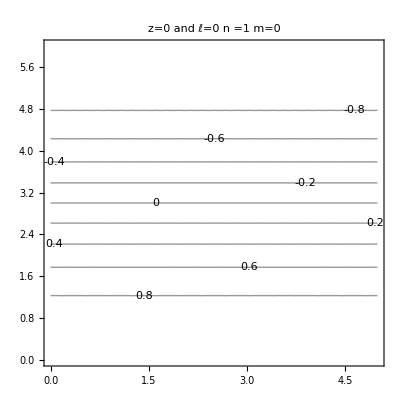
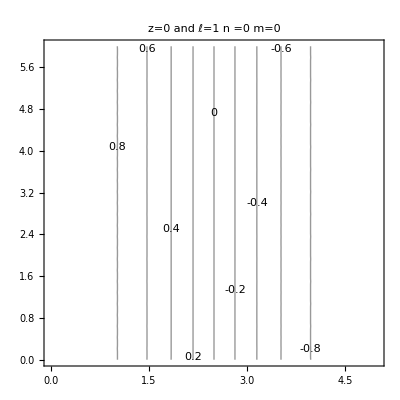
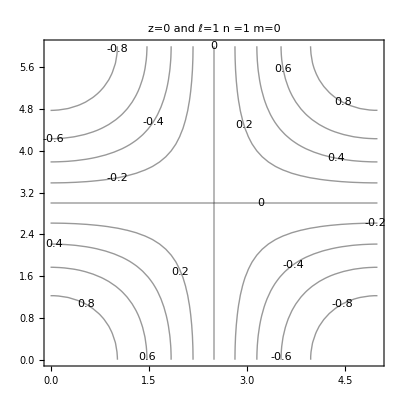
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

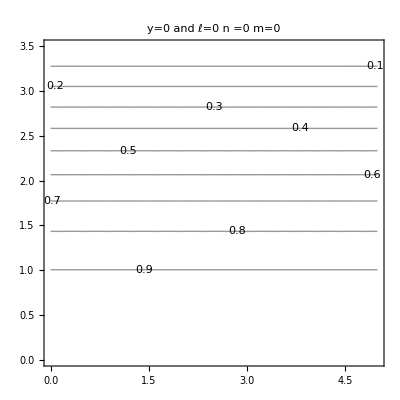
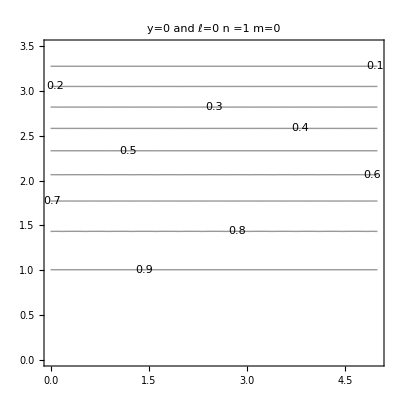
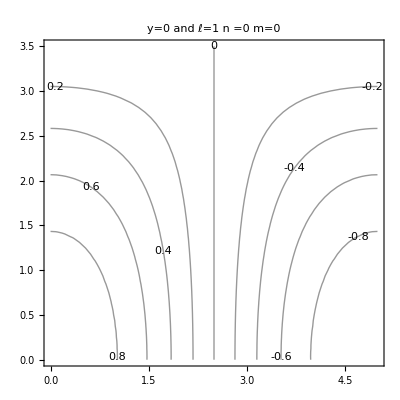
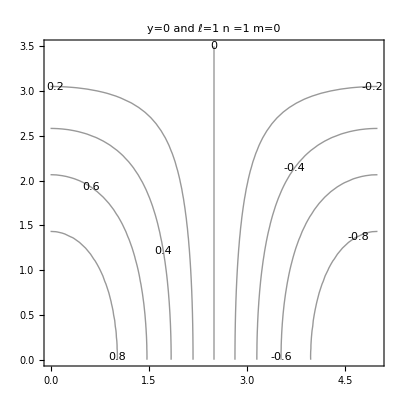

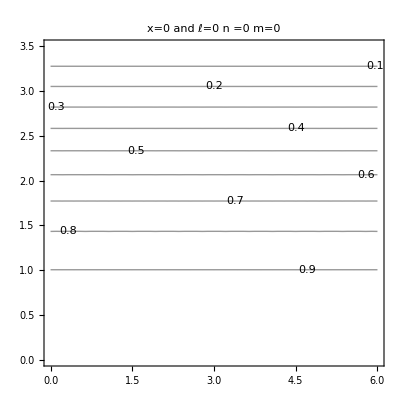
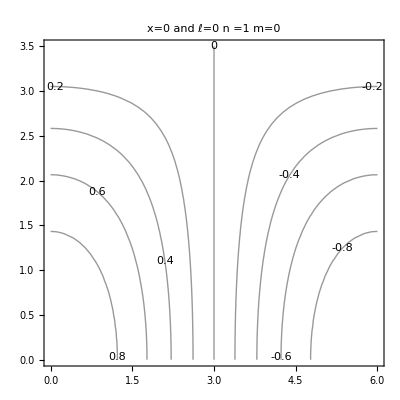
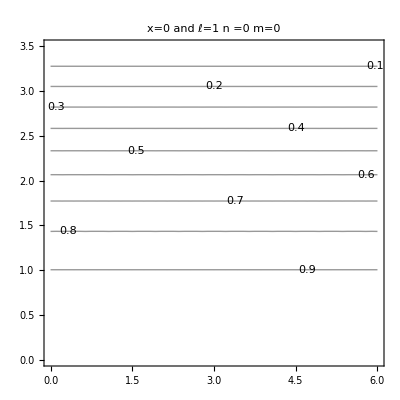
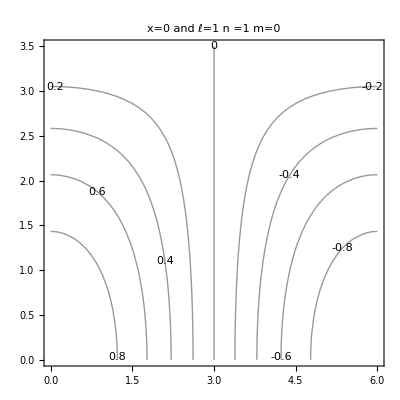

```mathematica
Table[ContourPlot[ψ[x,y,0,lowest4[[i]]],{x,0,Lx},{y,0,Ly},ContourLabels->True,ContourShading->None,PlotLabel->"z=0 and "<>"ℓ="<>ToString[lowest4[[i,1]]]<>"  n ="<>ToString[lowest4[[i,2]]]<>"  m="<>ToString[lowest4[[i,3]]]],{i,1,4,1}]
Table[ContourPlot[ψ[x,0,z,lowest4[[i]]],{x,0,Lx},{z,0,Lz},ContourLabels->True,ContourShading->None,PlotLabel->"y=0 and "<>"ℓ="<>ToString[lowest4[[i,1]]]<>"  n ="<>ToString[lowest4[[i,2]]]<>"  m="<>ToString[lowest4[[i,3]]]],{i,1,4,1}]
Table[ContourPlot[ψ[0,y,z,lowest4[[i]]],{y,0,Ly},{z,0,Lz},ContourLabels->True,ContourShading->None,PlotLabel->"x=0 and "<>"ℓ="<>ToString[lowest4[[i,1]]]<>"  n ="<>ToString[lowest4[[i,2]]]<>"  m="<>ToString[lowest4[[i,3]]]],{i,1,4,1}]
```

9.8

9.9

9.10

Final Exam

### 1.)

### 2.)

```mathematica
tFinal[x_,y_,nn_]:=Sum[(2 (-1)^(n+1))/(n π Sinh[n π])*Sin[n π x]*Sinh[n π y],{n,1,nn}]-4/π^3*Sum[(Sin [π x] Sin [(2n-1) π y])/((2n-1)^3+(2n-1)),{n,1,nn}]
```

```mathematica
ShowLegend[DensityPlot[tFinal[x,y,100],{x,0,1},{y,0,1},ColorFunction->"BlueGreenYellow",PlotPoints->70,PlotLabel->"n="<>ToString[100],PlotRange->{-.01,.85},AspectRatio->Automatic],{ColorData["BlueGreenYellow"][1-#1]&,10," hot","cold",LegendPosition->{.5,-.4}}]
```

-Graphics-